```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.0001,1,0]],B:=Inverse[β[ω,0.0001,1,0]],T1:=T1[1]},Do[J=Inverse[IdentityMatrix[14]-B.ConjugateTranspose[T1].J.T1].B,10000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Abs[Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]]
```

```mathematica
Timing[tr[1.001,0.0001,1,0]]
```

{1.11094,2.99936}

```mathematica
4000*1.11094/60
```

74.0627

```mathematica
pp=Table[{ω,tr[ω,0.0001,1,0]},{ω,Range[0,4,0.01]}]
```

{{0.,2.8×10^-7},{0.01,2.8081×10^-7},{0.02,2.83264×10^-7},{0.03,2.87439×10^-7},{0.04,2.93463×10^-7},{0.05,3.01536×10^-7},{0.06,3.11935×10^-7},{0.07,3.25045×10^-7},{0.08,3.41391×10^-7},{0.09,3.61694×10^-7},{0.1,3.86954×10^-7},{0.11,4.18578×10^-7},{0.12,4.58598×10^-7},{0.13,5.10023×10^-7},{0.14,5.77474×10^-7},{0.15,6.68349×10^-7},{0.16,7.95126×10^-7},{0.17,9.803×10^-7},{0.18,1.26801×10^-6},{0.19,1.75544×10^-6},{0.2,2.69447×10^-6},{0.21,4.92698×10^-6},{0.22,0.0000129427},{0.23,0.000120119},{0.24,0.999916},{0.25,0.999991},{0.26,0.999997},{0.27,0.999998},{0.28,0.999999},{0.29,0.999998},{0.3,0.999998},{0.31,0.999999},{0.32,0.999997},{0.33,0.999996},{0.34,0.999992},{0.35,0.999991},{0.36,0.999979},{0.37,1.},{0.38,0.999977},{0.39,0.999993},{0.4,1.},{0.41,1.00011},{0.42,1.99989},{0.43,1.99999},{0.44,1.99996},{0.45,1.99997},{0.46,1.99993},{0.47,1.99995},{0.48,2.},{0.49,1.99991},{0.5,1.99997},{0.51,1.99996},{0.52,1.99987},{0.53,1.99983},{0.54,1.99991},{0.55,1.99993},{0.56,1.99994},{0.57,1.99984},{0.58,1.99974},{0.59,1.99973},{0.6,2.},{0.61,1.99955},{0.62,1.99989},{0.63,1.99989},{0.64,1.99968},{0.65,1.99982},{0.66,1.99948},{0.67,1.99991},{0.68,1.99989},{0.69,1.99954},{0.7,1.99927},{0.71,1.99967},{0.72,1.99949},{0.73,1.99989},{0.74,1.99976},{0.75,1.99905},{0.76,1.99897},{0.77,1.99942},{0.78,1.999},{0.79,1.99988},{0.8,1.99966},{0.81,1.99912},{0.82,1.99884},{0.83,1.99924},{0.84,1.99955},{0.85,2.99948},{0.86,2.99989},{0.87,2.99905},{0.88,2.99958},{0.89,2.99872},{0.9,2.99894},{0.91,2.99892},{0.92,2.99869},{0.93,2.99929},{0.94,2.99986},{0.95,2.99869},{0.96,2.99996},{0.97,2.99879},{0.98,2.99943},{0.99,2.99974},{1.,2.99861},{1.01,2.99969},{1.02,2.99935},{1.03,2.99878},{1.04,2.99987},{1.05,2.99862},{1.06,2.99977},{1.07,2.99896},{1.08,2.99893},{1.09,2.99979},{1.1,2.99998},{1.11,2.99971},{1.12,2.99981},{1.13,2.99885},{1.14,2.99929},{1.15,2.99907},{1.16,2.99979},{1.17,2.99976},{1.18,2.99993},{1.19,2.99926},{1.2,2.9984},{1.21,2.99863},{1.22,2.99904},{1.23,2.99903},{1.24,2.99859},{1.25,2.9997},{1.26,2.99975},{1.27,2.9993},{1.28,2.99816},{1.29,2.99987},{1.3,2.9997},{1.31,2.99907},{1.32,2.99969},{1.33,2.99842},{1.34,2.99909},{1.35,2.99822},{1.36,2.99867},{1.37,2.99857},{1.38,2.99862},{1.39,2.99974},{1.4,2.99909},{1.41,2.99947},{1.42,2.99872},{1.43,2.99916},{1.44,2.9989},{1.45,2.99892},{1.46,2.99899},{1.47,2.99912},{1.48,2.99832},{1.49,2.99967},{1.5,2.99925},{1.51,2.99903},{1.52,2.99909},{1.53,2.9993},{1.54,2.99814},{1.55,2.99972},{1.56,2.9995},{1.57,2.99849},{1.58,2.99995},{1.59,2.99892},{1.6,2.99918},{1.61,2.99872},{1.62,2.99952},{1.63,2.99876},{1.64,2.99882},{1.65,2.99946},{1.66,2.99967},{1.67,2.99913},{1.68,2.99845},{1.69,2.99951},{1.7,2.99872},{1.71,2.99986},{1.72,2.99979},{1.73,2.99983},{1.74,2.9991},{1.75,2.99962},{1.76,2.9987},{1.77,1.99889},{1.78,1.999},{1.79,1.99976},{1.8,1.99948},{1.81,1.99953},{1.82,1.99995},{1.83,1.99901},{1.84,1.99892},{1.85,1.99929},{1.86,1.99957},{1.87,1.99987},{1.88,1.99929},{1.89,1.99986},{1.9,1.99989},{1.91,1.99957},{1.92,1.99994},{1.93,1.99966},{1.94,1.99977},{1.95,1.99985},{1.96,1.99934},{1.97,1.99941},{1.98,1.99977},{1.99,1.99968},{2.,1.99971},{2.01,1.99976},{2.02,1.99964},{2.03,1.99979},{2.04,1.99944},{2.05,1.99959},{2.06,1.99946},{2.07,1.99998},{2.08,2.},{2.09,1.99975},{2.1,1.99992},{2.11,1.99982},{2.12,2.},{2.13,1.99961},{2.14,1.99986},{2.15,1.99989},{2.16,1.99972},{2.17,1.99983},{2.18,1.99982},{2.19,2.},{2.2,1.99988},{2.21,1.9998},{2.22,1.99979},{2.23,1.99981},{2.24,1.99983},{2.25,1.99984},{2.26,1.99983},{2.27,1.99983},{2.28,1.99992},{2.29,1.99997},{2.3,1.99991},{2.31,1.99987},{2.32,1.99988},{2.33,1.99998},{2.34,1.9999},{2.35,1.99993},{2.36,1.99998},{2.37,1.99998},{2.38,1.99995},{2.39,1.99997},{2.4,1.99993},{2.41,1.99986},{2.42,1.00005},{2.43,0.999975},{2.44,0.999973},{2.45,0.999975},{2.46,0.999974},{2.47,0.999979},{2.48,0.999999},{2.49,1.},{2.5,0.999996},{2.51,1.},{2.52,0.999991},{2.53,0.999999},{2.54,0.999998},{2.55,0.999994},{2.56,0.999998},{2.57,0.999997},{2.58,0.999999},{2.59,1.},{2.6,0.999998},{2.61,0.999999},{2.62,1.},{2.63,1.},{2.64,0.999999},{2.65,1.},{2.66,1.},{2.67,1.},{2.68,1.},{2.69,1.},{2.7,1.},{2.71,1.},{2.72,1.},{2.73,1.},{2.74,1.},{2.75,1.},{2.76,1.},{2.77,1.},{2.78,0.999999},{2.79,0.999999},{2.8,0.999999},{2.81,0.999998},{2.82,0.999997},{2.83,0.999992},{2.84,0.999958},{2.85,0.000496198},{2.86,0.0000165305},{2.87,4.97473×10^-6},{2.88,2.35363×10^-6},{2.89,1.36412×10^-6},{2.9,8.87821×10^-7},{2.91,6.22951×10^-7},{2.92,4.6079×10^-7},{2.93,3.54437×10^-7},{2.94,2.8098×10^-7},{2.95,2.28152×10^-7},{2.96,1.88907×10^-7},{2.97,1.58966×10^-7},{2.98,1.35611×10^-7},{2.99,1.17044×10^-7},{3.,1.02043×10^-7},{3.01,8.97514×10^-8},{3.02,7.9554×10^-8},{3.03,7.10012×10^-8},{3.04,6.37576×10^-8},{3.05,5.75691×10^-8},{3.06,5.22402×10^-8},{3.07,4.76186×10^-8},{3.08,4.35846×10^-8},{3.09,4.00423×10^-8},{3.1,3.69149×10^-8},{3.11,3.414×10^-8},{3.12,3.16663×10^-8},{3.13,2.94518×10^-8},{3.14,2.74614×10^-8},{3.15,2.56657×10^-8},{3.16,2.40401×10^-8},{3.17,2.25637×10^-8},{3.18,2.12187×10^-8},{3.19,1.99899×10^-8},{3.2,1.88644×10^-8},{3.21,1.78307×10^-8},{3.22,1.68791×10^-8},{3.23,1.60012×10^-8},{3.24,1.51895×10^-8},{3.25,1.44374×10^-8},{3.26,1.37393×10^-8},{3.27,1.30901×10^-8},{3.28,1.24853×10^-8},{3.29,1.1921×10^-8},{3.3,1.13935×10^-8},{3.31,1.08998×10^-8},{3.32,1.0437×10^-8},{3.33,1.00026×10^-8},{3.34,9.59432×10^-9},{3.35,9.21007×10^-9},{3.36,8.84801×10^-9},{3.37,8.50646×10^-9},{3.38,8.1839×10^-9},{3.39,7.87895×10^-9},{3.4,7.59034×10^-9},{3.41,7.31692×10^-9},{3.42,7.05766×10^-9},{3.43,6.81158×10^-9},{3.44,6.5778×10^-9},{3.45,6.35553×10^-9},{3.46,6.14401×10^-9},{3.47,5.94257×10^-9},{3.48,5.75058×10^-9},{3.49,5.56745×10^-9},{3.5,5.39265×10^-9},{3.51,5.22569×10^-9},{3.52,5.06609×10^-9},{3.53,4.91344×10^-9},{3.54,4.76734×10^-9},{3.55,4.62743×10^-9},{3.56,4.49335×10^-9},{3.57,4.36479×10^-9},{3.58,4.24145×10^-9},{3.59,4.12306×10^-9},{3.6,4.00935×10^-9},{3.61,3.90008×10^-9},{3.62,3.79503×10^-9},{3.63,3.69399×10^-9},{3.64,3.59674×10^-9},{3.65,3.50311×10^-9},{3.66,3.41293×10^-9},{3.67,3.32601×10^-9},{3.68,3.24222×10^-9},{3.69,3.1614×10^-9},{3.7,3.08341×10^-9},{3.71,3.00813×10^-9},{3.72,2.93544×10^-9},{3.73,2.86521×10^-9},{3.74,2.79734×10^-9},{3.75,2.73172×10^-9},{3.76,2.66827×10^-9},{3.77,2.60687×10^-9},{3.78,2.54746×10^-9},{3.79,2.48994×10^-9},{3.8,2.43423×10^-9},{3.81,2.38026×10^-9},{3.82,2.32797×10^-9},{3.83,2.27728×10^-9},{3.84,2.22812×10^-9},{3.85,2.18045×10^-9},{3.86,2.13419×10^-9},{3.87,2.08931×10^-9},{3.88,2.04573×10^-9},{3.89,2.00342×10^-9},{3.9,1.96232×10^-9},{3.91,1.92239×10^-9},{3.92,1.88359×10^-9},{3.93,1.84588×10^-9},{3.94,1.80921×10^-9},{3.95,1.77355×10^-9},{3.96,1.73887×10^-9},{3.97,1.70512×10^-9},{3.98,1.67227×10^-9},{3.99,1.64031×10^-9},{4.,1.60918×10^-9}}

```mathematica
Pri=Table[{ω,Interpolation[pp][ω]},{ω,Range[0,4,0.001]}]
```

{{0.,2.8×10^-7},{0.001,2.80009×10^-7},{0.002,2.80034×10^-7},{0.003,2.80075×10^-7},{0.004,2.80131×10^-7},{0.005,2.80204×10^-7},{0.006,2.80293×10^-7},{0.007,2.80398×10^-7},{0.008,2.80519×10^-7},{0.009,2.80656×10^-7},{0.01,2.8081×10^-7},{0.011,2.8098×10^-7},3978,{3.99,1.64031×10^-9},{3.991,1.63716×10^-9},{3.992,1.63401×10^-9},{3.993,1.63088×10^-9},{3.994,1.62776×10^-9},{3.995,1.62464×10^-9},{3.996,1.62153×10^-9},{3.997,1.61843×10^-9},{3.998,1.61534×10^-9},{3.999,1.61226×10^-9},{4.,1.60918×10^-9}}
 |  |  |  |

```mathematica
Pri[[3001]]
```

{3.,1.02043×10^-7}

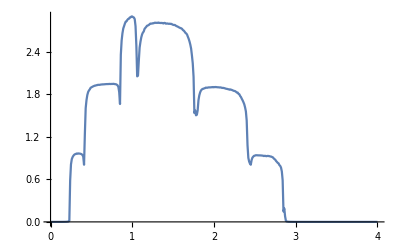

```mathematica
ListLinePlot[Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/2imp/2imp5.csv"]]
```

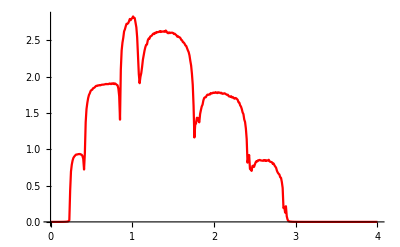

```mathematica
ListLinePlot[Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/2imp/2imp7.csv"],PlotStyle->Red]
```

```mathematica
{Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/2imp/2imp3.csv"][[101]],Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/2imp/2imp4.csv"][[101]],Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/2imp/2imp5.csv"][[101]],Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/2imp/2imp6.csv"][[101]],Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/2imp/2imp7.csv"][[101]],Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/2imp/2imp8.csv"][[101]],Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/2imp/2imp9.csv"][[101]]}
```

{{1.,2.95736},{1.,2.93117},{1.,2.89482},{1.,2.84975},{1.,2.80909},{1.,2.7654},{1.,2.7087}}

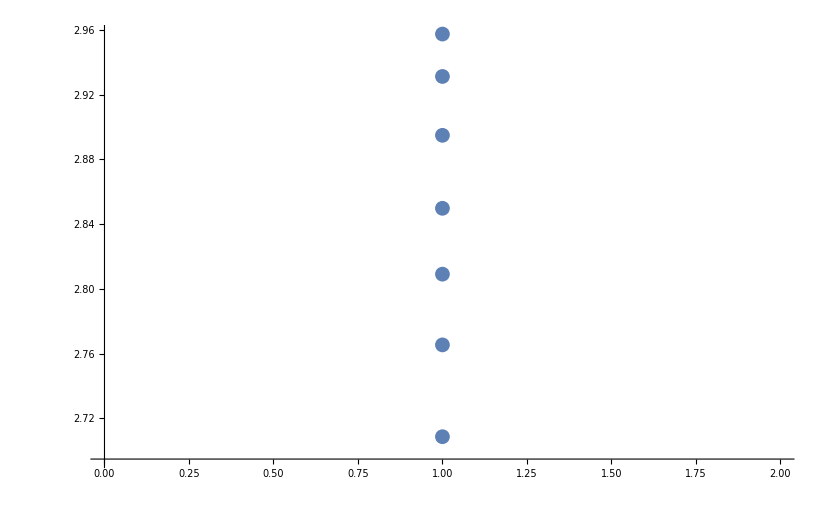

```mathematica
ListPlot[{{1.,2.9573615115376977},{1.,2.93117140503726},{1.,2.8948219516568523},{1.,2.8497496073102124},{1.,2.8090850848663202},{1.,2.7654004479767758},{1.,2.7087012441097627}}]
```

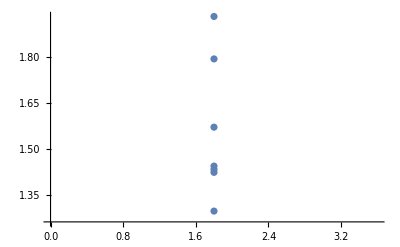

```mathematica
ListPlot[{{1.8,1.9323284881743383},{1.8,1.7935609609250351},{1.8,1.570493630467822},{1.8,1.4227491731282012},{1.8,1.432755373918663},{1.8,1.4433158261926406},{1.8,1.2962064032847274}}]
```

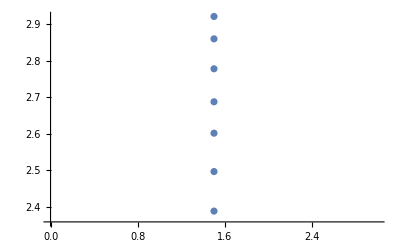

```mathematica
ListPlot[{{1.5,2.9201981912549586},{1.5,2.859081813908485},{1.5,2.777444669451055},{1.5,2.687431419797386},{1.5,2.6018040662695023},{1.5,2.4971110264760643},{1.5,2.3892834734134683}}]
```

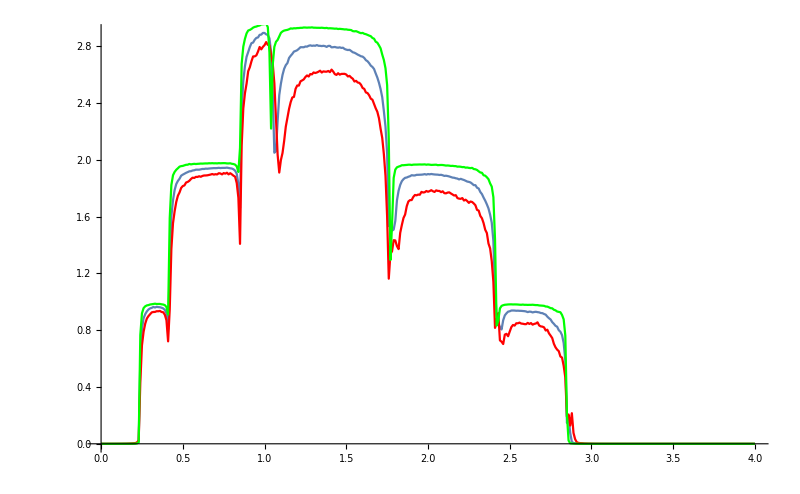

```mathematica
Show[%1,%3,ListLinePlot[Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/2imp/2imp3.csv"],PlotStyle->Green]]
```

```mathematica
f2:=f2=Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/2imp/2imp5.csv"]]
f3:=f3=Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/3imp/3imp5.csv"]]
 f4:=f4=Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/4imp/4imp5.csv"]]
 f5:=f5=Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/5imp/5imp5.csv"]]
 f6:=f6=Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/6imp/6imp5.csv"]]
 f7:=f7=Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/7imp/7imp5.csv"]]
 f8:=f8=Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/8imp/8imp5.csv"]]
 f9:=f9=Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/9imp/9imp5.csv"]]
 f10:=f10=Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/10imp/10imp5.csv"]]
 f11:=f11=Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/11imp/11imp5.csv"]]
 f12:=f12=Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/12imp/12imp5.csv"]]
```

```mathematica
k2:=k2=Table[{ω,f2[ω]},{ω,0,4,0.001}]
k3:=k3=Table[{ω,f3[ω]},{ω,0,4,0.001}]
k4:=k4=Table[{ω,f4[ω]},{ω,0,4,0.001}]
k5:=k5=Table[{ω,f5[ω]},{ω,0,4,0.001}]
k6:=k6=Table[{ω,f6[ω]},{ω,0,4,0.001}]
k7:=k7=Table[{ω,f7[ω]},{ω,0,4,0.001}]
k8:=k8=Table[{ω,f8[ω]},{ω,0,4,0.001}]
k9:=k9=Table[{ω,f9[ω]},{ω,0,4,0.001}]
k10:=k10=Table[{ω,f10[ω]},{ω,0,4,0.001}]
k11:=k11=Table[{ω,f11[ω]},{ω,0,4,0.001}]
```

```mathematica
Clear[k2,k3,k4,k5,k6,k7,k8,k9,k10,k11]
```

```mathematica
f[ω_]:={{2,k2[[ω*1000+1]][[2]]},{3,k3[[ω*1000+1]][[2]]},{4,k4[[ω*1000+1]][[2]]},{5,k5[[ω*1000+1]][[2]]},{6,k6[[ω*1000+1]][ [2]]},{7,k7[[ω*1000+1]][[2]]},{8,k8[[ω*1000+1]][[2]]},{9,k9[[ω*1000+1]][[2]]},{10,k10[[ω*1000+1]][[2]]},{11,k11[[ω*1000+1]][[2]]}}
```

```mathematica
f[2.25]
```

{{0,1.99984},{2,1.69757},{3,1.60271},{4,1.52263},{5,1.43926},{6,1.40569},{7,1.36891},{8,1.35375},{9,1.30377},{10,1.27321},{11,1.25344}}

```mathematica
φ[ω_]:=Interpolation[f[ω]]
```

```mathematica
sloap[ω_,n_]:=Abs[(φ[ω][n]-φ[ω][n+.001])/0.001]
```

```mathematica
Clear[γ,s]
```

```mathematica
γ[ω_,n_]:=γ[ω,n]=(-2φ[ω][n]+φ[ω][n+0.1]+φ[ω][n-0.1])/(.1*.1)
```

InterpolatingFunction::dmval: Input value {1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.001} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

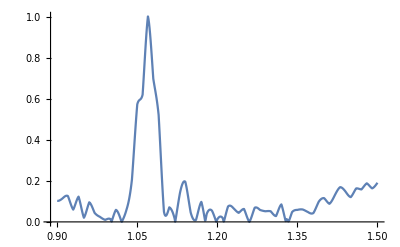

```mathematica
Show[ListLinePlot[Table[{ω,s[ω,1]},{ω,Range[0.9,1.5,0.001]}],PlotRange->All](*,ListLinePlot[Table[γ[ω,1.5],{ω,Range[0.9,1.5,0.01]}],PlotRange->All,PlotStyle->Red]*)]
```

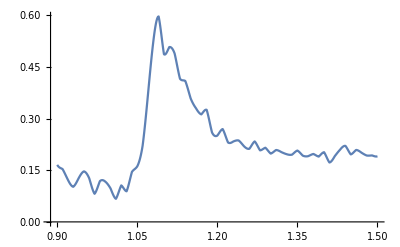

-Graphics-

```mathematica
Clear[s]
```

```mathematica
s[ω_,l_]:=s[ω,l]=Mean[Table[sloap[ω,k],{k,Range[1,l,0.01]}]]
```

```mathematica
deltae[ϵ1_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,7}],μ2=RandomInteger[{1,7}],μ3=RandomInteger[{1,7}],μ4=RandomInteger[{1,7}],μ5=RandomInteger[{8,14}],μ6=RandomInteger[{8,14}],μ7=RandomInteger[{8,14}],μ8=RandomInteger[{8,14}]},
tra:=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}(*,{μ8,μ8}*)}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}(*,{μ7,μ7}*)}->ω+ⅈ*0.0001-0]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}(*,{μ6,μ6}*)}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-0]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp1,imp4,imp3,imp2}]};
Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,4}]; J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];Table[{ω,If[tra>3,3,tra]},{ω,Range[0,4,0.01]}]]
```

```mathematica
Table[Table[{ω,Interpolation[%544[[δ]]][ω]},{ω,0,4,0.001}],{δ,100}]
```

{{{0.,2.75462×10^-7},{0.001,0.000347317},{0.002,0.000635386},{0.003,0.000868239},{0.004,0.00104963},{0.005,0.00118331},{0.006,0.00127303},{0.007,0.00132256},{0.008,0.00133563},{0.009,0.00131601},{0.01,0.00126746},{0.011,0.00119372},3978,{3.99,0.0000187959},{3.991,0.0000195391},{3.992,0.00001985},{3.993,0.0000196722},{3.994,0.0000189491},{3.995,0.0000176245},{3.996,0.0000156418},{3.997,0.0000129445},{3.998,9.47641×10^-6},{3.999,5.18091×10^-6},{4.,1.60922×10^-9}},98,{1}}
 |  |  |  |

```mathematica
Table[deltae[0.7],100]
```

{{{0.,2.75462×10^-7},{0.01,0.00126746},{0.02,0.0000161102},{0.03,2.41218×10^-7},{0.04,2.45879×10^-6},{0.05,0.000329409},{0.06,4.54067×10^-6},{0.07,0.000368307},{0.08,0.000576874},{0.09,0.00141747},{0.1,0.000408818},{0.11,0.000502617},377,{3.89,2.00492×10^-9},{3.9,1.9624×10^-9},{3.91,0.0000259632},{3.92,1.88359×10^-9},{3.93,1.84588×10^-9},{3.94,1.80927×10^-9},{3.95,5.96874×10^-8},{3.96,1.7399×10^-9},{3.97,5.3761×10^-8},{3.98,1.67227×10^-9},{3.99,0.0000187959},{4.,1.60922×10^-9}},98,{1}}
 |  |  |  |

```mathematica
ns[lim1_,lim2_,δ_,k_]:=NIntegrate[Interpolation[Table[{ω,s[ω,k]*(Pri[[ω*1000+1]][[2]]-%545[[δ]][[ω*1000+1]][[2]])},{ω,Range[lim1,lim2,0.001]}]][ω],{ω,lim1,lim2}]/(NIntegrate[Interpolation[Table[{ω,(s[ω,k]*s[ω,k]+0*Abs[γ[ω,k]]*(Pri[[ω*1000+1]][[2]]-%545[[δ]][[ω*1000+1]][[2]]))},{ω,Range[lim1,lim2,0.001]}]][ω],{ω,lim1,lim2}])
```

```mathematica
nss[lim1_,lim2_,δ_,k_]:=NIntegrate[Interpolation[Table[{ω,s[ω,2]*(Pri[[ω*1000+1]][[2]]-%545[[δ]][[ω*1000+1]][[2]])},{ω,Range[lim1,lim2,0.001]}]][ω],{ω,lim1,lim2}]/(NIntegrate[Interpolation[Table[{ω,(s[ω,2]*s[ω,2]+2*Abs[γ[ω,k]]*(Pri[[ω*1000+1]][[2]]-%545[[δ]][[ω*1000+1]][[2]]))},{ω,Range[lim1,lim2,0.001]}]][ω],{ω,lim1,lim2}])
```

```mathematica
Table[ns[0.9,1.5,k,2],{k,100}]
```

{2.35086,1.95617,2.26371,2.60158,2.78014,2.35184,1.68414,1.57811,2.2811,2.33338,2.36264,2.42124,2.29668,2.63045,2.89531,2.13879,2.42113,2.15096,2.2192,2.18705,2.52961,2.13505,1.2957,1.87307,2.21966,2.32287,2.36742,2.31849,2.71396,2.24638,2.59972,2.20042,1.72419,2.29744,2.01648,2.22153,2.86958,1.95766,2.18669,2.81082,2.13222,1.25391,2.34911,2.07519,2.17833,1.97009,2.12094,2.2255,2.28118,2.76014,2.54054,2.32949,2.30814,2.74415,2.3781,2.22077,2.64846,1.93213,2.73757,1.90364,1.92411,1.75354,1.94959,2.64289,2.16659,1.79448,2.56198,2.20192,1.70828,2.18647,2.85524,2.15053,2.65023,1.99319,2.74727,2.56041,2.78652,1.19378,2.19381,2.15823,2.29064,2.08361,1.70033,2.74187,1.86793,1.71361,2.42899,2.76017,1.654,2.18001,2.20491,1.7116,1.9893,1.0215,2.25225,1.67734,2.23586,1.26035,1.97081,1.97337}

```mathematica
Around[%556]
```

2.20.4

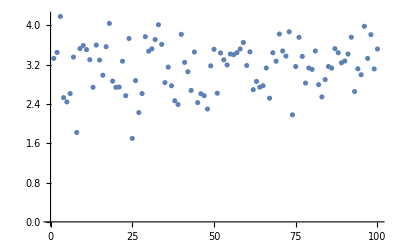

```mathematica
ListPlot[%522]
```

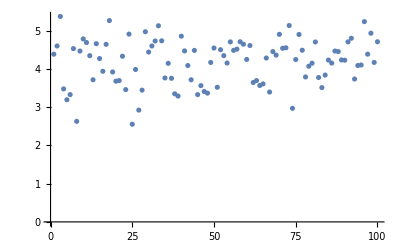

```mathematica
ListPlot[%519]
```

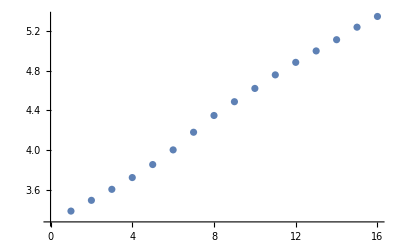

```mathematica
ListPlot[%517]
```

```mathematica
Misfit[lim1_,lim2_,δ_,k_]:=NIntegrate[Interpolation[Table[{ω,(tr[ω,0.0001,1,0]-%479[[δ]][[ω*100+1]][[2]])^2},{ω,Range[lim1,lim2,0.01]}]][ω],{ω,lim1,lim2}]+2*k*NIntegrate[Interpolation[Table[{ω,Mean[s[ω,0.01]]*(tr[ω,0.0001,1,0]-%479[[δ]][[ω*100+1]][[2]])},{ω,Range[lim1,lim2,0.01]}]][ω],{ω,lim1,lim2}]+2*k*k*NIntegrate[Interpolation[Table[{ω,(Mean[s[ω,0.01]]*Mean[s[ω,0.01]]+2γ[ω,k]*(tr[ω,0.0001,1,0]-%479[[δ]][[ω*100+1]][[2]]))},{ω,Range[lim1,lim2,0.01]}]][ω],{ω,lim1,lim2}]/100
```

```mathematica
misfit1[lim1_,lim2_,δ_,k_,ϵ1_,x_,y_]:=Module[{Tin=T1[1],T=TT[1]},
υ=Module[{},
ρ1:=Module[{B1=Transpose[{%479[[δ]][[1;;4000]][[;;,1]],(%479[[δ]][[1;;4000,2]]-Pri[[1;;4000,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ2:=Module[{B1=Transpose[{%479[[δ]][[1;;4000]][[;;,1]],(%479[[δ]][[1;;4000,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/2imp/2imp7.csv"][[1;;4000,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ3:=Module[{B1=Transpose[{%479[[δ]][[1;;4000]][[;;,1]],(%479[[δ]][[1;;4000,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/3imp/3imp7.csv"][[1;;4000,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ4:=Module[{B1=Transpose[{%479[[δ]][[1;;4000]][[;;,1]],(%479[[δ]][[1;;4000,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/4imp/4imp7.csv"][[1;;4000,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ5:=Module[{B1=Transpose[{%479[[δ]][[1;;4000]][[;;,1]],(%479[[δ]][[1;;4000,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/5imp/5imp7.csv"][[1;;4000,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ6:=Module[{B1=Transpose[{%479[[δ]][[1;;4000]][[;;,1]],(%479[[δ]][[1;;4000,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/6imp/6imp7.csv"][[1;;4000,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ7:=Module[{B1=Transpose[{%479[[δ]][[1;;4000]][[;;,1]],(%479[[δ]][[1;;4000,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/7imp/7imp7.csv"][[1;;4000,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ8:=Module[{B1=Transpose[{%479[[δ]][[1;;4000]][[;;,1]],(%479[[δ]][[1;;4000,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/8imp/8imp7.csv"][[1;;4000,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ9:=Module[{B1=Transpose[{%479[[δ]][[1;;4000]][[;;,1]],(%479[[δ]][[1;;4000,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/9imp/9imp7.csv"][[1;;4000,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ10:=Module[{B1=Transpose[{%479[[δ]][[1;;4000]][[;;,1]],(%479[[δ]][[1;;4000,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/10imp/10imp7.csv"][[1;;4000,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ11:=Module[{B1=Transpose[{%479[[δ]][[1;;4000]][[;;,1]],(%479[[δ]][[1;;4000,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/11imp/11imp7.csv"][[1;;4000,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
list:={{1,ρ1},{2,ρ2},{3,ρ3},{4,ρ4},{5,ρ5},{6,ρ6},{7,ρ7},{8,ρ8},{9,ρ9},{10,ρ10},{11,ρ11}};
{list[[Position[list,Min[list]][[1,1]],1]],NIntegrate[Interpolation[Table[{ω,s[ω,4]*(Pri[[ω*1000+1]][[2]]-%479[[δ]][[ω*1000+1]][[2]])},{ω,Range[lim1,lim2,0.001]}]][ω],{ω,lim1,lim2}]/(NIntegrate[Interpolation[Table[{ω,(s[ω,4]*s[ω,4]+0*γ[ω,k]*(Pri[[ω*1000+1]][[2]]-%479[[δ]][[ω*1000+1]][[2]]))},{ω,Range[lim1,lim2,0.001]}]][ω],{ω,lim1,lim2}]),NIntegrate[Interpolation[Table[{ω,s[ω,0]*(Pri[[ω*1000+1]][[2]]-%479[[δ]][[ω*1000+1]][[2]])},{ω,Range[lim1,lim2,0.001]}]][ω],{ω,lim1,lim2}]/(NIntegrate[Interpolation[Table[{ω,(s[ω,0]*s[ω,0]+2*γ[ω,k]*(Pri[[ω*1000+1]][[2]]-%479[[δ]][[ω*1000+1]][[2]]))},{ω,Range[lim1,lim2,0.001]}]][ω],{ω,lim1,lim2}])(*,{ρ1,ρ2,ρ3,ρ4,ρ5,ρ6,ρ7,ρ8,ρ9,ρ10,ρ11}*)}];
υ]
```

```mathematica
misfit1[0.9,1.5,12,1,0.7,1.5,0.9]
```

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

$Aborted[]

```mathematica
Table[{k,Table[misfit1[0.9,1.5,δ,k,0.7,1.5,0.9][[3]],{δ,Range[1,100,1]}]},{k,Range[0.5,8,0.5]}]
```

{{0.5,{1.66352,2.03146,2.14736,1.89998,1.97954,2.13187,2.06422,1.74005,1.89101,1.80409,1.96543,1.98046,1.6114,2.10356,1.59033,2.07303,1.99334,1.89681,2.04945,1.81683,1.51507,2.02219,1.90197,1.98865,2.07823,1.97304,1.98279,1.90347,1.83062,2.09846,1.92488,2.10473,1.74303,1.96787,1.72433,1.76993,1.94153,2.08275,2.04148,1.90918,1.94756,1.75207,1.75428,2.04741,1.591,1.48457,1.77474,1.88258,1.98736,1.93786,1.96624,2.12503,1.91264,2.13581,2.0915,1.85121,1.80558,1.90564,1.95694,1.76091,2.03923,2.12435,1.89434,2.14091,2.00597,1.86278,1.77186,2.03736,2.05929,1.59033,1.6888,2.06665,1.68454,2.1161,1.22689,2.00116,1.95912,2.03395,1.78356,1.59652,1.90348,2.16512,2.11748,2.10861,1.99323,2.04832,2.02973,2.02765,1.51315,1.82175,1.94979,1.59652,2.08269,1.97988,2.03533,2.16523,1.84239,1.95083,1.93089,2.13762}},{1.,{1.59582,1.92575,2.00327,1.86942,1.83331,2.01278,2.02845,1.67806,1.83069,1.78861,1.89218,1.89156,1.57496,2.00327,1.53109,1.95105,1.93101,1.81877,1.96409,1.69279,1.44766,1.91422,1.81731,1.9186,1.95346,1.88068,1.91649,1.85226,1.77023,2.03757,1.81137,2.00771,1.66068,1.86217,1.69783,1.69462,1.88005,2.00015,1.96206,1.8443,1.87723,1.7054,1.66505,1.92603,1.54509,1.41139,1.68094,1.81573,1.95424,1.83764,1.91197,2.0097,1.83897,2.04056,1.99483,1.7381,1.7433,1.81282,1.85358,1.70269,1.913,1.98551,1.81257,2.04552,1.97126,1.79725,1.71265,1.93263,2.01483,1.53109,1.6471,1.95279,1.62592,2.01312,1.21579,1.89387,1.83672,1.97011,1.75623,1.55138,1.85568,2.08029,2.02746,2.02837,1.95638,1.93682,1.97818,1.97378,1.45406,1.78395,1.8471,1.55138,1.99687,1.87199,1.96095,2.04831,1.72508,1.89655,1.88249,2.04387}},{1.5,{1.53342,1.83049,1.87731,1.83983,1.7072,1.90629,1.9939,1.62033,1.7741,1.77339,1.82419,1.8103,1.54012,1.91211,1.47612,1.84263,1.87246,1.74689,1.88555,1.58461,1.386,1.81719,1.73987,1.85333,1.84282,1.79658,1.85448,1.80375,1.7137,1.98011,1.71051,1.91924,1.58576,1.76725,1.67213,1.62545,1.82235,1.92385,1.8886,1.78369,1.8118,1.66115,1.58446,1.81823,1.50177,1.34509,1.59656,1.75347,1.92222,1.74727,1.86061,1.90624,1.77076,1.95345,1.9067,1.63802,1.68517,1.72862,1.7606,1.64819,1.80148,1.86371,1.73757,1.95826,1.93774,1.73616,1.65727,1.83813,1.97225,1.47612,1.60741,1.85082,1.57124,1.9197,1.20489,1.7975,1.72871,1.91015,1.72973,1.50871,1.81023,2.00186,1.94477,1.95401,1.92087,1.83683,1.92918,1.92269,1.39941,1.74769,1.75468,1.50871,1.91785,1.77524,1.89181,1.94337,1.62182,1.84521,1.83647,1.95799}},{2.,{1.47571,1.74422,1.76624,1.81116,1.59732,1.8105,1.96051,1.56645,1.7209,1.75843,1.76092,1.73574,1.5068,1.82888,1.42495,1.74563,1.81736,1.68048,1.81306,1.48942,1.32938,1.72953,1.66877,1.79235,1.74404,1.71968,1.79636,1.7577,1.66067,1.92581,1.62029,1.83823,1.51731,1.68154,1.6472,1.56171,1.76808,1.85316,1.82044,1.72693,1.75079,1.61914,1.51131,1.72187,1.4608,1.28474,1.52025,1.69534,1.89123,1.66537,1.81194,1.81292,1.70743,1.87346,1.82603,1.54884,1.63079,1.6519,1.67649,1.59708,1.70225,1.75599,1.66852,1.87815,1.90534,1.6791,1.60536,1.75245,1.93143,1.42495,1.56959,1.75898,1.52012,1.83457,1.19418,1.71046,1.63271,1.85373,1.70402,1.46833,1.76695,1.92912,1.86857,1.88491,1.88663,1.74665,1.88255,1.87418,1.34871,1.71288,1.67107,1.46833,1.84484,1.68801,1.82739,1.84866,1.53022,1.79657,1.79264,1.87904}},{2.5,{1.42219,1.66571,1.66759,1.78337,1.50073,1.72388,1.92821,1.51603,1.6708,1.74372,1.70189,1.66707,1.47488,1.7526,1.37721,1.65832,1.7654,1.61894,1.74593,1.40502,1.27721,1.64993,1.60324,1.73526,1.65531,1.64909,1.74177,1.71395,1.61082,1.8744,1.53911,1.76379,1.45452,1.60375,1.623,1.50278,1.71695,1.78748,1.75703,1.67367,1.69374,1.57921,1.44461,1.6352,1.42201,1.22958,1.4509,1.64094,1.86122,1.59081,1.76575,1.7283,1.64847,1.79977,1.75191,1.46887,1.57981,1.5817,1.60006,1.54904,1.61338,1.66005,1.60476,1.80433,1.874,1.62566,1.5566,1.6744,1.89227,1.37721,1.53351,1.67582,1.47223,1.75666,1.18366,1.63146,1.5468,1.80055,1.67906,1.43006,1.72569,1.86149,1.79811,1.82053,1.85358,1.66492,1.83812,1.82806,1.30157,1.67942,1.59506,1.43006,1.77718,1.60894,1.7672,1.76275,1.44842,1.75044,1.75085,1.80622}},{3.,{0.194646,0.201195,0.152838,0.279806,0.140561,0.174402,0.307284,0.210324,0.201674,0.459883,0.229283,0.183903,0.308019,0.208644,0.196088,0.16935,0.225433,0.227489,0.189921,0.135112,0.146498,0.171043,0.186436,0.220687,0.19111,0.204811,0.222441,0.261822,0.195185,0.239555,0.164096,0.178232,0.160736,0.166434,0.264849,0.201768,0.263441,0.212367,0.191778,0.187963,0.223097,0.258593,0.166253,0.169376,0.201748,0.135197,0.16546,0.195124,0.29833,0.18468,0.27567,0.18691,0.197119,0.202816,0.1993,0.151542,0.230821,0.206032,0.183569,0.225978,0.172251,0.158956,0.190058,0.201364,0.289438,0.229648,0.234118,0.1927,0.236546,0.196088,0.210236,0.168045,0.186937,0.182356,0.637009,0.172919,0.160261,0.206282,0.276477,0.221514,0.260969,0.222989,0.210665,0.194731,0.27661,0.176596,0.273367,0.265426,0.184481,0.26011,0.173373,0.221514,0.219979,0.172415,0.212221,0.186031,0.144706,0.261613,0.251234,0.186715}},{3.5,{1.60807,1.90807,2.04353,2.05003,1.80284,2.07556,2.20324,1.72457,1.98778,1.86849,1.94423,1.98854,1.58703,2.03165,1.55216,1.97954,2.06945,1.81734,2.10519,1.68662,1.50595,1.97832,1.88239,2.02067,1.89524,1.8917,2.03297,1.93859,1.91007,2.20666,1.81008,2.16337,1.72642,1.92112,1.85281,1.70163,1.92232,2.10435,2.12757,2.02759,1.9505,1.76084,1.68197,1.94084,1.62995,1.45632,1.68803,1.94694,2.12703,1.84453,1.98494,2.03973,1.94123,2.13342,2.0643,1.74035,1.77884,1.78533,1.85829,1.74953,1.88707,2.00588,1.87855,2.14561,2.15618,1.8427,1.74472,1.94762,2.27668,1.55216,1.78768,2.02693,1.71653,2.12367,1.19304,1.94063,1.82572,2.17892,1.9134,1.60821,1.96322,2.18815,2.11427,2.22331,2.1441,1.97703,2.09791,2.09322,1.46361,1.91729,1.88474,1.60821,2.06156,1.90384,2.08638,2.09839,1.72798,1.986,2.01657,2.20689}},{4.,{-0.212223,-0.234776,-0.135146,-0.311553,-0.129437,-0.162402,-0.384993,-0.231364,-0.186159,-3.49406,-0.257551,-0.171366,-0.65473,-0.22752,-0.218863,-0.162447,-0.22889,-0.287653,-0.173692,-0.123585,-0.130825,-0.159624,-0.183025,-0.221886,-0.216392,-0.225925,-0.235692,-0.314106,-0.179269,-0.252053,-0.160009,-0.156821,-0.144819,-0.154644,-0.300513,-0.225244,-0.348907,-0.213641,-0.172688,-0.166388,-0.239795,-0.361798,-0.163378,-0.161872,-0.202245,-0.118239,-0.163606,-0.184578,-0.37949,-0.196016,-0.372914,-0.188573,-0.192787,-0.203163,-0.202191,-0.14606,-0.276513,-0.23752,-0.188358,-0.261885,-0.17288,-0.145372,-0.190017,-0.199316,-0.341171,-0.253347,-0.286156,-0.202924,-0.21961,-0.218863,-0.205791,-0.153497,-0.186722,-0.169171,0.465207,-0.165369,-0.153435,-0.188327,-0.325439,-0.262552,-0.309515,-0.230084,-0.218623,-0.173604,-0.307482,-0.167794,-0.335573,-0.311295,-0.207205,-0.297177,-0.164428,-0.262552,-0.234538,-0.166097,-0.209251,-0.182122,-0.135157,-0.328388,-0.276147,-0.167055}},{4.5,{1.76949,2.18364,2.30365,2.30838,2.02164,2.35221,2.52102,1.91602,2.22114,2.11704,2.1853,2.23206,1.75925,2.31778,1.70894,2.2464,2.34202,2.04811,2.37791,1.88552,1.64073,2.23337,2.1114,2.26014,2.15295,2.13271,2.31703,2.1734,2.1216,2.53918,2.02832,2.44952,1.90033,2.16216,2.07365,1.88795,2.16779,2.38871,2.40158,2.27689,2.19121,1.98582,1.86668,2.18308,1.7849,1.57961,1.87553,2.18603,2.44081,2.08849,2.25681,2.32599,2.18348,2.44076,2.35316,1.9596,1.98573,1.99078,2.08588,1.94669,2.12228,2.26128,2.11202,2.45451,2.46268,2.03844,1.94183,2.20931,2.58971,1.70894,1.98681,2.29088,1.91924,2.41789,1.29827,2.19064,2.04015,2.4758,2.15182,1.78417,2.21343,2.49949,2.42125,2.52519,2.43668,2.22097,2.3949,2.37842,1.60941,2.15236,2.10318,1.78417,2.33596,2.14078,2.36128,2.39308,1.93653,2.25909,2.27473,2.50808}},{5.,{0.224973,0.34724,0.14227,0.359953,0.13755,0.178461,0.536563,0.26151,0.189774,-1.18172,0.300115,0.180817,1.34004,0.282087,0.24366,0.186442,0.261069,0.394226,0.182844,0.137281,0.12981,0.174383,0.202634,0.230171,0.276371,0.268771,0.302712,0.359445,0.181022,0.32763,0.176344,0.164374,0.143171,0.16784,0.36286,0.249481,0.461221,0.242604,0.181491,0.173879,0.270326,0.624508,0.176953,0.17445,0.201669,0.11634,0.177176,0.200525,0.613227,0.245545,0.574021,0.224129,0.216637,0.244595,0.237996,0.170107,0.330769,0.263383,0.213777,0.307304,0.191163,0.153815,0.216918,0.238277,0.465128,0.249933,0.335862,0.249943,0.240769,0.24366,0.223984,0.164503,0.218712,0.187544,-0.31988,0.186343,0.164355,0.208633,0.421905,0.325367,0.388333,0.273137,0.269916,0.183011,0.385388,0.179212,0.467861,0.398278,0.237808,0.346691,0.170141,0.325367,0.275232,0.181065,0.233567,0.210402,0.147931,0.472377,0.320275,0.176744}},{5.5,{1.81709,2.17069,2.40383,2.3949,2.0922,2.43547,2.59557,1.95985,2.33945,2.11934,2.24798,2.32998,1.77215,2.36922,1.73877,2.29553,2.42411,2.06718,2.50038,1.90891,1.69573,2.31051,2.17258,2.37286,2.1773,2.18124,2.35092,2.25206,2.22693,2.59355,2.08103,2.58042,1.99041,2.23475,2.1238,1.93647,2.21722,2.47553,2.5241,2.38482,2.26468,1.98281,1.91164,2.26375,1.8512,1.63048,1.92307,2.26423,2.47538,2.10485,2.28733,2.37741,2.24495,2.4982,2.41944,1.97755,2.02823,2.05314,2.13489,1.98585,2.18659,2.35968,2.16156,2.51371,2.52434,2.14463,1.98722,2.23821,2.71571,1.73877,2.04374,2.38696,1.94447,2.50956,1.28562,2.24471,2.10529,2.57322,2.19404,1.80226,2.26762,2.57918,2.47583,2.66748,2.50788,2.3089,2.4463,2.44235,1.62505,2.22251,2.19769,1.80226,2.4055,2.21265,2.45075,2.46059,1.98326,2.29253,2.35469,2.64503}},{6.,{-0.391211,-0.733693,-0.251685,-0.631645,-0.228413,-0.318746,-0.974502,-0.487164,-0.324146,2.75371,-0.514263,-0.29321,-2.0276,-0.468075,-0.471947,-0.36444,-0.453407,-0.704998,-0.310589,-0.277908,-0.248426,-0.304401,-0.384281,-0.358064,-0.440421,-0.422107,-0.624102,-0.519512,-0.315974,-0.630095,-0.311365,-0.285664,-0.254597,-0.30563,-0.713938,-0.42335,-0.671468,-0.405077,-0.311127,-0.318385,-0.454167,-1.7771,-0.316925,-0.290884,-0.362157,-0.2276,-0.321778,-0.37159,-1.13684,-0.503047,-1.00979,-0.382697,-0.432331,-0.458055,-0.406255,-0.359221,-0.593152,-0.385094,-0.375229,-0.622465,-0.318146,-0.259186,-0.423037,-0.430039,-0.819671,-0.340207,-0.568965,-0.496945,-0.455416,-0.471947,-0.449465,-0.287587,-0.499779,-0.338024,0.487941,-0.353332,-0.28835,-0.399128,-0.966116,-0.742698,-0.68402,-0.495785,-0.469471,-0.312562,-0.758829,-0.294378,-0.782749,-0.753651,-0.491726,-0.522002,-0.270918,-0.742698,-0.480648,-0.311989,-0.398522,-0.383893,-0.261549,-0.842477,-0.52402,-0.291321}},{6.5,{1.95358,2.24443,3.01936,2.55685,2.4802,2.88424,2.68914,2.10064,2.74129,1.945,2.39724,2.68451,1.70528,2.52666,1.85175,2.67634,2.67332,2.10648,2.97754,2.28206,2.0203,2.70024,2.47173,2.63752,2.26649,2.29895,2.54047,2.33158,2.61156,2.80509,2.36353,3.19921,2.39793,2.64052,2.23684,2.06302,2.235,2.74794,3.02243,2.88778,2.44902,1.98333,2.14124,2.61038,2.05504,1.98293,2.16484,2.60775,2.50022,2.2866,2.29908,2.62398,2.56056,2.79545,2.67188,2.28032,2.11887,2.15043,2.35226,2.10874,2.44934,2.84515,2.42633,2.8094,2.61716,2.2825,2.06163,2.45045,3.18799,1.85175,2.28603,2.86983,2.16812,2.97564,1.15688,2.59649,2.44001,3.0487,2.30345,1.88427,2.36262,2.86292,2.68969,3.24353,2.68308,2.65639,2.50792,2.58076,1.72069,2.30835,2.52344,1.88427,2.6199,2.53577,2.74807,2.81781,2.30306,2.33636,2.50741,3.19138}},{7.,{0.163925,0.150238,0.218731,0.203432,0.163889,0.206456,0.19801,0.177605,0.229112,0.133075,0.177017,0.17942,0.132301,0.167359,0.168261,0.213781,0.192592,0.153067,0.219624,0.20012,0.229885,0.192341,0.214694,0.18129,0.137763,0.148763,0.194349,0.161938,0.232179,0.196361,0.180131,0.237061,0.243342,0.210432,0.186914,0.165012,0.151559,0.188504,0.223658,0.250854,0.184293,0.162199,0.170689,0.18157,0.202583,0.24444,0.183422,0.215916,0.167143,0.178534,0.16492,0.163366,0.236803,0.195258,0.182788,0.209287,0.172347,0.145233,0.166997,0.189468,0.168332,0.195268,0.203973,0.18578,0.177866,0.152778,0.16597,0.181785,0.27313,0.168261,0.222467,0.210937,0.217777,0.219518,0.11165,0.200135,0.18669,0.2513,0.196946,0.17988,0.183804,0.205672,0.17363,0.236014,0.209576,0.17127,0.171259,0.199431,0.160038,0.159422,0.169285,0.17988,0.185244,0.183267,0.195569,0.202498,0.173858,0.164393,0.184479,0.210274}},{7.5,{2.51377,3.3519,4.02733,3.4705,3.32335,3.96143,3.84555,2.75431,3.50103,2.84957,3.29672,3.65919,2.31615,3.59643,2.36628,3.62237,3.72519,2.93485,3.96983,2.96846,2.37984,3.66745,3.21055,3.59838,3.33391,3.25727,3.58157,3.20551,3.2735,4.10457,3.11674,4.25814,2.84723,3.46905,3.01568,2.69408,3.15053,3.83725,4.03747,3.72211,3.30192,2.73052,2.79452,3.50488,2.51908,2.30079,2.76827,3.4472,3.7476,3.15057,3.26147,3.85822,3.31383,4.02466,3.73991,2.95971,2.81156,2.92212,3.25052,2.7535,3.33578,3.81152,3.2235,4.10331,3.86261,3.04833,2.71774,3.45773,4.27388,2.36628,2.90936,3.83197,2.79238,4.06676,1.48675,3.53496,3.19891,4.11756,3.15213,2.42712,3.2097,4.05738,3.95112,4.36504,3.76773,3.71573,3.62635,3.59529,2.19599,3.20766,3.39172,2.42712,3.68954,3.41427,3.79574,3.92696,3.00856,3.34873,3.43054,4.39121}},{8.,{-0.049824,-0.0434052,-0.0533437,-0.0525435,-0.0511366,-0.0516908,-0.0505444,-0.0499853,-0.0564649,-0.0432587,-0.0498488,-0.0517614,-0.0441494,-0.0492499,-0.0493174,-0.0514921,-0.0507867,-0.0464484,-0.0552166,-0.0489686,-0.0554729,-0.0525715,-0.0536607,-0.0517518,-0.044838,-0.0463001,-0.048927,-0.0498764,-0.0560293,-0.0496509,-0.050223,-0.0556358,-0.0586662,-0.0526492,-0.0497833,-0.0502313,-0.0480619,-0.0518869,-0.0550727,-0.0555995,-0.0510355,-0.0460514,-0.0486606,-0.0514601,-0.0536736,-0.0554056,-0.0503757,-0.053132,-0.0465819,-0.0477381,-0.0482341,-0.0471653,-0.0542797,-0.049824,-0.0506468,-0.0502114,-0.0494733,-0.0488063,-0.0477157,-0.0509259,-0.0499814,-0.0531074,-0.0513778,-0.0495584,-0.048401,-0.0510951,-0.0497166,-0.0472952,-0.0567116,-0.0493174,-0.0526469,-0.0533677,-0.0514036,-0.0538145,-0.0419907,-0.05053,-0.0518712,-0.0550848,-0.0499792,-0.0488968,-0.0504041,-0.0518653,-0.048642,-0.0553953,-0.0514526,-0.0496886,-0.0486679,-0.05086,-0.0473627,-0.0484404,-0.0509803,-0.0488968,-0.0492679,-0.0514154,-0.0521788,-0.051731,-0.0497748,-0.0470472,-0.0513007,-0.0540935}}}

```mathematica
Table[Around[%422[[x,2]]],{x,16}]
```

{1.920.18,1.840.17,1.770.16,1.700.15,1.640.15,0.210.06,1.910.20,-0.250.34,2.150.25,0.250.22,2.220.27,-0.50.4,2.50.4,0.1890.029,3.30.6,-0.05060.0030}

```mathematica
Dimensions[%422]
```

{16,2}

```mathematica
Table[%418[[x]][[3]],{x,100}]
```

{3,4,5,4,4,5,5,3,4,4,4,4,3,5,3,4,5,4,5,3,3,4,4,4,4,4,5,4,4,5,4,5,3,4,4,3,4,5,5,4,4,4,3,4,3,2,3,4,5,4,5,5,4,5,5,3,4,4,4,3,4,4,4,5,5,4,4,4,5,3,3,4,3,5,2,4,4,5,4,3,4,5,5,5,5,4,5,5,3,4,4,3,5,4,5,5,3,4,4,5}

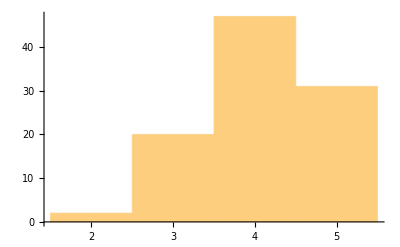

```mathematica
Histogram[%416]
```

```mathematica
Histogram[%411]
```

-Graphics-

```mathematica
Around[%407]
```

3.30.6

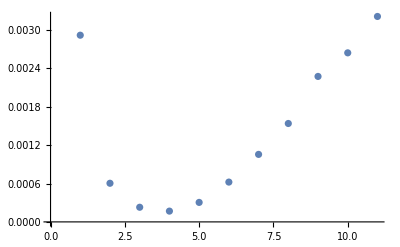
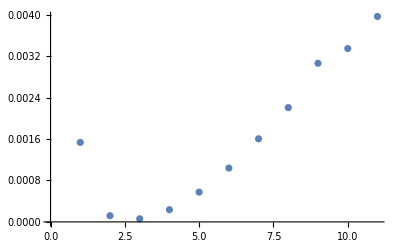
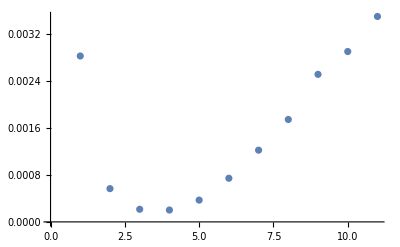
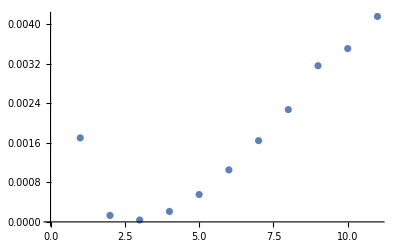
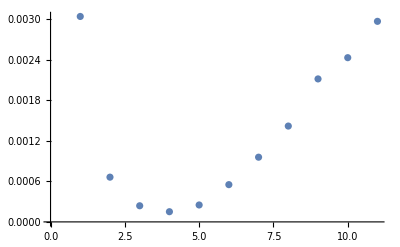
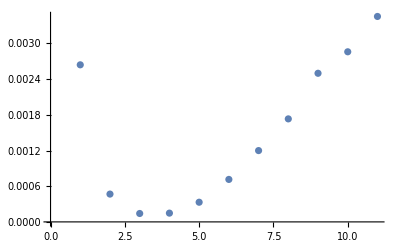
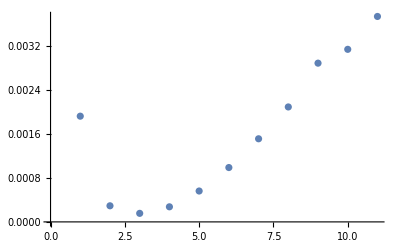
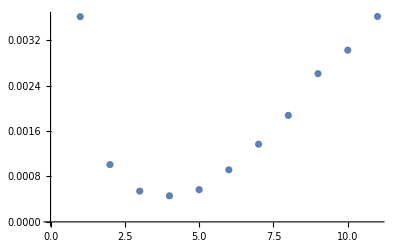
{{{-Graphics-,4,0.000168599,3.27424,1.75608,{0.00291813,0.000603875,0.000228814,0.000168599,0.000304645,0.000622284,0.00105526,0.00153817,0.00227369,0.00264246,0.00321111}},{-Graphics-,4,0.000168599,3.47675,1.68136,{0.00291813,0.000603875,0.000228814,0.000168599,0.000304645,0.000622284,0.00105526,0.00153817,0.00227369,0.00264246,0.00321111}},{-Graphics-,4,0.000168599,3.7118,0.227071,{0.00291813,0.000603875,0.000228814,0.000168599,0.000304645,0.000622284,0.00105526,0.00153817,0.00227369,0.00264246,0.00321111}},{-Graphics-,4,0.000168599,3.99335,-0.223396,{0.00291813,0.000603875,0.000228814,0.000168599,0.000304645,0.000622284,0.00105526,0.00153817,0.00227369,0.00264246,0.00321111}},{-Graphics-,4,0.000168599,4.21777,0.244688,{0.00291813,0.000603875,0.000228814,0.000168599,0.000304645,0.000622284,0.00105526,0.00153817,0.00227369,0.00264246,0.00321111}},{-Graphics-,4,0.000168599,4.41693,-0.496792,{0.00291813,0.000603875,0.000228814,0.000168599,0.000304645,0.000622284,0.00105526,0.00153817,0.00227369,0.00264246,0.00321111}},{-Graphics-,4,0.000168599,4.59129,0.250484,{0.00291813,0.000603875,0.000228814,0.000168599,0.000304645,0.000622284,0.00105526,0.00153817,0.00227369,0.00264246,0.00321111}},{-Graphics-,4,0.000168599,4.7803,-0.0555427,{0.00291813,0.000603875,0.000228814,0.000168599,0.000304645,0.000622284,0.00105526,0.00153817,0.00227369,0.00264246,0.00321111}}},{{-Graphics-,3,0.0000601362,2.33702,1.50552,{0.00153385,0.00011966,0.0000601362,0.000235627,0.000574321,0.00103827,0.00160364,0.00220563,0.00306113,0.00334567,0.00396476}},{-Graphics-,3,0.0000601362,2.51378,1.40604,{0.00153385,0.00011966,0.0000601362,0.000235627,0.000574321,0.00103827,0.00160364,0.00220563,0.00306113,0.00334567,0.00396476}},{-Graphics-,3,0.0000601362,2.71223,0.195845,{0.00153385,0.00011966,0.0000601362,0.000235627,0.000574321,0.00103827,0.00160364,0.00220563,0.00306113,0.00334567,0.00396476}},{-Graphics-,3,0.0000601362,2.94126,-0.217765,{0.00153385,0.00011966,0.0000601362,0.000235627,0.000574321,0.00103827,0.00160364,0.00220563,0.00306113,0.00334567,0.00396476}},{-Graphics-,3,0.0000601362,3.13071,0.248406,{0.00153385,0.00011966,0.0000601362,0.000235627,0.000574321,0.00103827,0.00160364,0.00220563,0.00306113,0.00334567,0.00396476}},{-Graphics-,3,0.0000601362,3.30577,-0.553029,{0.00153385,0.00011966,0.0000601362,0.000235627,0.000574321,0.00103827,0.00160364,0.00220563,0.00306113,0.00334567,0.00396476}},{-Graphics-,3,0.0000601362,3.45922,0.188583,{0.00153385,0.00011966,0.0000601362,0.000235627,0.000574321,0.00103827,0.00160364,0.00220563,0.00306113,0.00334567,0.00396476}},{-Graphics-,3,0.0000601362,3.61888,-0.050131,{0.00153385,0.00011966,0.0000601362,0.000235627,0.000574321,0.00103827,0.00160364,0.00220563,0.00306113,0.00334567,0.00396476}}},{{-Graphics-,4,0.000202576,3.21441,1.75892,{0.00283183,0.00056758,0.000215775,0.000202576,0.000371913,0.000745104,0.00122432,0.00174824,0.00251833,0.00290799,0.00350661}},{-Graphics-,4,0.000202576,3.4233,1.62554,{0.00283183,0.00056758,0.000215775,0.000202576,0.000371913,0.000745104,0.00122432,0.00174824,0.00251833,0.00290799,0.00350661}},{-Graphics-,4,0.000202576,3.65147,0.179374,{0.00283183,0.00056758,0.000215775,0.000202576,0.000371913,0.000745104,0.00122432,0.00174824,0.00251833,0.00290799,0.00350661}},{-Graphics-,4,0.000202576,3.90628,-0.167898,{0.00283183,0.00056758,0.000215775,0.000202576,0.000371913,0.000745104,0.00122432,0.00174824,0.00251833,0.00290799,0.00350661}},{-Graphics-,4,0.000202576,4.11684,0.18302,{0.00283183,0.00056758,0.000215775,0.000202576,0.000371913,0.000745104,0.00122432,0.00174824,0.00251833,0.00290799,0.00350661}},{-Graphics-,4,0.000202576,4.28792,-0.364523,{0.00283183,0.00056758,0.000215775,0.000202576,0.000371913,0.000745104,0.00122432,0.00174824,0.00251833,0.00290799,0.00350661}},{-Graphics-,4,0.000202576,4.44189,0.238268,{0.00283183,0.00056758,0.000215775,0.000202576,0.000371913,0.000745104,0.00122432,0.00174824,0.00251833,0.00290799,0.00350661}},{-Graphics-,4,0.000202576,4.6127,-0.0544806,{0.00283183,0.00056758,0.000215775,0.000202576,0.000371913,0.000745104,0.00122432,0.00174824,0.00251833,0.00290799,0.00350661}}},{{-Graphics-,3,0.0000380927,2.51154,1.52557,{0.0017006,0.000130464,0.0000380927,0.000211617,0.000554532,0.00105281,0.00164495,0.00227254,0.00316121,0.00350809,0.00415834}},{-Graphics-,3,0.0000380927,2.6804,1.42849,{0.0017006,0.000130464,0.0000380927,0.000211617,0.000554532,0.00105281,0.00164495,0.00227254,0.00316121,0.00350809,0.00415834}},{-Graphics-,3,0.0000380927,2.86731,0.186098,{0.0017006,0.000130464,0.0000380927,0.000211617,0.000554532,0.00105281,0.00164495,0.00227254,0.00316121,0.00350809,0.00415834}},{-Graphics-,3,0.0000380927,3.07944,-0.185189,{0.0017006,0.000130464,0.0000380927,0.000211617,0.000554532,0.00105281,0.00164495,0.00227254,0.00316121,0.00350809,0.00415834}},{-Graphics-,3,0.0000380927,3.25321,0.191099,{0.0017006,0.000130464,0.0000380927,0.000211617,0.000554532,0.00105281,0.00164495,0.00227254,0.00316121,0.00350809,0.00415834}},{-Graphics-,3,0.0000380927,3.39973,-0.364674,{0.0017006,0.000130464,0.0000380927,0.000211617,0.000554532,0.00105281,0.00164495,0.00227254,0.00316121,0.00350809,0.00415834}},{-Graphics-,3,0.0000380927,3.53287,0.205553,{0.0017006,0.000130464,0.0000380927,0.000211617,0.000554532,0.00105281,0.00164495,0.00227254,0.00316121,0.00350809,0.00415834}},{-Graphics-,3,0.0000380927,3.67547,-0.0533574,{0.0017006,0.000130464,0.0000380927,0.000211617,0.000554532,0.00105281,0.00164495,0.00227254,0.00316121,0.00350809,0.00415834}}},{{-Graphics-,4,0.000150958,3.31178,1.84689,{0.00304258,0.000662628,0.000238918,0.000150958,0.000250603,0.000551814,0.000958316,0.0014194,0.00211757,0.00243214,0.00297034}},{-Graphics-,4,0.000150958,3.54712,1.68915,{0.00304258,0.000662628,0.000238918,0.000150958,0.000250603,0.000551814,0.000958316,0.0014194,0.00211757,0.00243214,0.00297034}},{-Graphics-,4,0.000150958,3.80574,0.186522,{0.00304258,0.000662628,0.000238918,0.000150958,0.000250603,0.000551814,0.000958316,0.0014194,0.00211757,0.00243214,0.00297034}},{-Graphics-,4,0.000150958,4.09666,-0.181947,{0.00304258,0.000662628,0.000238918,0.000150958,0.000250603,0.000551814,0.000958316,0.0014194,0.00211757,0.00243214,0.00297034}},{-Graphics-,4,0.000150958,4.33502,0.194158,{0.00304258,0.000662628,0.000238918,0.000150958,0.000250603,0.000551814,0.000958316,0.0014194,0.00211757,0.00243214,0.00297034}},{-Graphics-,4,0.000150958,4.53721,-0.350289,{0.00304258,0.000662628,0.000238918,0.000150958,0.000250603,0.000551814,0.000958316,0.0014194,0.00211757,0.00243214,0.00297034}},{-Graphics-,4,0.000150958,4.72112,0.214098,{0.00304258,0.000662628,0.000238918,0.000150958,0.000250603,0.000551814,0.000958316,0.0014194,0.00211757,0.00243214,0.00297034}},{-Graphics-,4,0.000150958,4.91792,-0.0543666,{0.00304258,0.000662628,0.000238918,0.000150958,0.000250603,0.000551814,0.000958316,0.0014194,0.00211757,0.00243214,0.00297034}}},{{-Graphics-,3,0.000141232,3.11244,1.75449,{0.00264089,0.000467659,0.000141232,0.000147403,0.000330697,0.000714083,0.00119899,0.00173195,0.00249852,0.00285987,0.00345383}},{-Graphics-,3,0.000141232,3.32581,1.60075,{0.00264089,0.000467659,0.000141232,0.000147403,0.000330697,0.000714083,0.00119899,0.00173195,0.00249852,0.00285987,0.00345383}},{-Graphics-,3,0.000141232,3.55561,0.170428,{0.00264089,0.000467659,0.000141232,0.000147403,0.000330697,0.000714083,0.00119899,0.00173195,0.00249852,0.00285987,0.00345383}},{-Graphics-,3,0.000141232,3.80773,-0.161294,{0.00264089,0.000467659,0.000141232,0.000147403,0.000330697,0.000714083,0.00119899,0.00173195,0.00249852,0.00285987,0.00345383}},{-Graphics-,3,0.000141232,4.01827,0.175215,{0.00264089,0.000467659,0.000141232,0.000147403,0.000330697,0.000714083,0.00119899,0.00173195,0.00249852,0.00285987,0.00345383}},{-Graphics-,3,0.000141232,4.18906,-0.331306,{0.00264089,0.000467659,0.000141232,0.000147403,0.000330697,0.000714083,0.00119899,0.00173195,0.00249852,0.00285987,0.00345383}},{-Graphics-,3,0.000141232,4.34471,0.207581,{0.00264089,0.000467659,0.000141232,0.000147403,0.000330697,0.000714083,0.00119899,0.00173195,0.00249852,0.00285987,0.00345383}},{-Graphics-,3,0.000141232,4.51368,-0.0522926,{0.00264089,0.000467659,0.000141232,0.000147403,0.000330697,0.000714083,0.00119899,0.00173195,0.00249852,0.00285987,0.00345383}}},{{-Graphics-,3,0.000155604,2.56037,1.58237,{0.00192507,0.000293264,0.000155604,0.000274747,0.000562377,0.000989742,0.00151355,0.00209301,0.00289033,0.00314217,0.00374063}},{-Graphics-,3,0.000155604,2.74643,1.47824,{0.00192507,0.000293264,0.000155604,0.000274747,0.000562377,0.000989742,0.00151355,0.00209301,0.00289033,0.00314217,0.00374063}},{-Graphics-,3,0.000155604,2.95531,0.19588,{0.00192507,0.000293264,0.000155604,0.000274747,0.000562377,0.000989742,0.00151355,0.00209301,0.00289033,0.00314217,0.00374063}},{-Graphics-,3,0.000155604,3.19636,-0.20855,{0.00192507,0.000293264,0.000155604,0.000274747,0.000562377,0.000989742,0.00151355,0.00209301,0.00289033,0.00314217,0.00374063}},{-Graphics-,3,0.000155604,3.39563,0.228887,{0.00192507,0.000293264,0.000155604,0.000274747,0.000562377,0.000989742,0.00151355,0.00209301,0.00289033,0.00314217,0.00374063}},{-Graphics-,3,0.000155604,3.57721,-0.372736,{0.00192507,0.000293264,0.000155604,0.000274747,0.000562377,0.000989742,0.00151355,0.00209301,0.00289033,0.00314217,0.00374063}},{-Graphics-,3,0.000155604,3.74114,0.148941,{0.00192507,0.000293264,0.000155604,0.000274747,0.000562377,0.000989742,0.00151355,0.00209301,0.00289033,0.00314217,0.00374063}},{-Graphics-,3,0.000155604,3.90411,-0.0477693,{0.00192507,0.000293264,0.000155604,0.000274747,0.000562377,0.000989742,0.00151355,0.00209301,0.00289033,0.00314217,0.00374063}}},{{-Graphics-,4,0.000459454,3.56404,1.84103,{0.00361344,0.00100912,0.000541824,0.000459454,0.000567596,0.000917931,0.00136856,0.00187587,0.0026103,0.00302418,0.00361774}},{-Graphics-,4,0.000459454,3.78685,1.68671,{0.00361344,0.00100912,0.000541824,0.000459454,0.000567596,0.000917931,0.00136856,0.00187587,0.0026103,0.00302418,0.00361774}},{-Graphics-,4,0.000459454,4.02577,0.171215,{0.00361344,0.00100912,0.000541824,0.000459454,0.000567596,0.000917931,0.00136856,0.00187587,0.0026103,0.00302418,0.00361774}},{-Graphics-,4,0.000459454,4.28644,-0.153587,{0.00361344,0.00100912,0.000541824,0.000459454,0.000567596,0.000917931,0.00136856,0.00187587,0.0026103,0.00302418,0.00361774}},{-Graphics-,4,0.000459454,4.50166,0.161156,{0.00361344,0.00100912,0.000541824,0.000459454,0.000567596,0.000917931,0.00136856,0.00187587,0.0026103,0.00302418,0.00361774}},{-Graphics-,4,0.000459454,4.6635,-0.284646,{0.00361344,0.00100912,0.000541824,0.000459454,0.000567596,0.000917931,0.00136856,0.00187587,0.0026103,0.00302418,0.00361774}},{-Graphics-,4,0.000459454,4.81509,0.216583,{0.00361344,0.00100912,0.000541824,0.000459454,0.000567596,0.000917931,0.00136856,0.00187587,0.0026103,0.00302418,0.00361774}},{-Graphics-,4,0.000459454,4.98276,-0.054359,{0.00361344,0.00100912,0.000541824,0.000459454,0.000567596,0.000917931,0.00136856,0.00187587,0.0026103,0.00302418,0.00361774}}},{{-Graphics-,3,0.0000334325,2.7872,1.63583,{0.00208706,0.000240957,0.0000334325,0.00010474,0.000355802,0.000768044,0.00128083,0.00184122,0.00265082,0.00296804,0.00357185}},{-Graphics-,3,0.0000334325,2.97574,1.54053,{0.00208706,0.000240957,0.0000334325,0.00010474,0.000355802,0.000768044,0.00128083,0.00184122,0.00265082,0.00296804,0.00357185}},{-Graphics-,3,0.0000334325,3.18898,0.205499,{0.00208706,0.000240957,0.0000334325,0.00010474,0.000355802,0.000768044,0.00128083,0.00184122,0.00265082,0.00296804,0.00357185}},{-Graphics-,3,0.0000334325,3.43716,-0.20855,{0.00208706,0.000240957,0.0000334325,0.00010474,0.000355802,0.000768044,0.00128083,0.00184122,0.00265082,0.00296804,0.00357185}},{-Graphics-,3,0.0000334325,3.63783,0.217608,{0.00208706,0.000240957,0.0000334325,0.00010474,0.000355802,0.000768044,0.00128083,0.00184122,0.00265082,0.00296804,0.00357185}},{-Graphics-,3,0.0000334325,3.81399,-0.390874,{0.00208706,0.000240957,0.0000334325,0.00010474,0.000355802,0.000768044,0.00128083,0.00184122,0.00265082,0.00296804,0.00357185}},{-Graphics-,3,0.0000334325,3.97242,0.198785,{0.00208706,0.000240957,0.0000334325,0.00010474,0.000355802,0.000768044,0.00128083,0.00184122,0.00265082,0.00296804,0.00357185}},{-Graphics-,3,0.0000334325,4.13827,-0.0534234,{0.00208706,0.000240957,0.0000334325,0.00010474,0.000355802,0.000768044,0.00128083,0.00184122,0.00265082,0.00296804,0.00357185}}},{{-Graphics-,3,0.000176393,3.07995,1.73296,{0.00262692,0.000490492,0.000176393,0.000177751,0.000362775,0.000732023,0.00120994,0.00173382,0.00250509,0.0028664,0.00345313}},{-Graphics-,3,0.000176393,3.28632,1.61093,{0.00262692,0.000490492,0.000176393,0.000177751,0.000362775,0.000732023,0.00120994,0.00173382,0.00250509,0.0028664,0.00345313}},{-Graphics-,3,0.000176393,3.51521,0.190946,{0.00262692,0.000490492,0.000176393,0.000177751,0.000362775,0.000732023,0.00120994,0.00173382,0.00250509,0.0028664,0.00345313}},{-Graphics-,3,0.000176393,3.77559,-0.187444,{0.00262692,0.000490492,0.000176393,0.000177751,0.000362775,0.000732023,0.00120994,0.00173382,0.00250509,0.0028664,0.00345313}},{-Graphics-,3,0.000176393,3.98799,0.206392,{0.00262692,0.000490492,0.000176393,0.000177751,0.000362775,0.000732023,0.00120994,0.00173382,0.00250509,0.0028664,0.00345313}},{-Graphics-,3,0.000176393,4.16932,-0.414015,{0.00262692,0.000490492,0.000176393,0.000177751,0.000362775,0.000732023,0.00120994,0.00173382,0.00250509,0.0028664,0.00345313}},{-Graphics-,3,0.000176393,4.33016,0.228246,{0.00262692,0.000490492,0.000176393,0.000177751,0.000362775,0.000732023,0.00120994,0.00173382,0.00250509,0.0028664,0.00345313}},{-Graphics-,3,0.000176393,4.5046,-0.0537816,{0.00262692,0.000490492,0.000176393,0.000177751,0.000362775,0.000732023,0.00120994,0.00173382,0.00250509,0.0028664,0.00345313}}},{{-Graphics-,4,0.000290309,3.23246,1.73146,{0.00290776,0.000637726,0.000295771,0.000290309,0.000476778,0.000873795,0.00136652,0.00191084,0.00270442,0.00309904,0.00371174}},{-Graphics-,4,0.000290309,3.42928,1.62568,{0.00290776,0.000637726,0.000295771,0.000290309,0.000476778,0.000873795,0.00136652,0.00191084,0.00270442,0.00309904,0.00371174}},{-Graphics-,4,0.000290309,3.64808,0.193652,{0.00290776,0.000637726,0.000295771,0.000290309,0.000476778,0.000873795,0.00136652,0.00191084,0.00270442,0.00309904,0.00371174}},{-Graphics-,4,0.000290309,3.89765,-0.177704,{0.00290776,0.000637726,0.000295771,0.000290309,0.000476778,0.000873795,0.00136652,0.00191084,0.00270442,0.00309904,0.00371174}},{-Graphics-,4,0.000290309,4.09776,0.176131,{0.00290776,0.000637726,0.000295771,0.000290309,0.000476778,0.000873795,0.00136652,0.00191084,0.00270442,0.00309904,0.00371174}},{-Graphics-,4,0.000290309,4.25541,-0.297784,{0.00290776,0.000637726,0.000295771,0.000290309,0.000476778,0.000873795,0.00136652,0.00191084,0.00270442,0.00309904,0.00371174}},{-Graphics-,4,0.000290309,4.40318,0.219408,{0.00290776,0.000637726,0.000295771,0.000290309,0.000476778,0.000873795,0.00136652,0.00191084,0.00270442,0.00309904,0.00371174}},{-Graphics-,4,0.000290309,4.56367,-0.0560399,{0.00290776,0.000637726,0.000295771,0.000290309,0.000476778,0.000873795,0.00136652,0.00191084,0.00270442,0.00309904,0.00371174}}},{{-Graphics-,2,0.0000854143,2.13354,1.3827,{0.0012864,0.0000854143,0.000138359,0.00044228,0.000899537,0.00151002,0.00220045,0.00291423,0.00390089,0.00425576,0.00496015}},{-Graphics-,2,0.0000854143,2.28533,1.26532,{0.0012864,0.0000854143,0.000138359,0.00044228,0.000899537,0.00151002,0.00220045,0.00291423,0.00390089,0.00425576,0.00496015}},{-Graphics-,2,0.0000854143,2.44415,0.151207,{0.0012864,0.0000854143,0.000138359,0.00044228,0.000899537,0.00151002,0.00220045,0.00291423,0.00390089,0.00425576,0.00496015}},{-Graphics-,2,0.0000854143,2.6119,-0.146014,{0.0012864,0.0000854143,0.000138359,0.00044228,0.000899537,0.00151002,0.00220045,0.00291423,0.00390089,0.00425576,0.00496015}},{-Graphics-,2,0.0000854143,2.75411,0.144562,{0.0012864,0.0000854143,0.000138359,0.00044228,0.000899537,0.00151002,0.00220045,0.00291423,0.00390089,0.00425576,0.00496015}},{-Graphics-,2,0.0000854143,2.86188,-0.273994,{0.0012864,0.0000854143,0.000138359,0.00044228,0.000899537,0.00151002,0.00220045,0.00291423,0.00390089,0.00425576,0.00496015}},{-Graphics-,2,0.0000854143,2.96491,0.19544,{0.0012864,0.0000854143,0.000138359,0.00044228,0.000899537,0.00151002,0.00220045,0.00291423,0.00390089,0.00425576,0.00496015}},{-Graphics-,2,0.0000854143,3.07783,-0.0536278,{0.0012864,0.0000854143,0.000138359,0.00044228,0.000899537,0.00151002,0.00220045,0.00291423,0.00390089,0.00425576,0.00496015}}},{{-Graphics-,3,0.0000691174,2.35294,1.45172,{0.00151067,0.000104502,0.0000691174,0.000257725,0.000617262,0.00109199,0.00167215,0.00228659,0.00316126,0.00346969,0.00410432}},{-Graphics-,3,0.0000691174,2.50488,1.41312,{0.00151067,0.000104502,0.0000691174,0.000257725,0.000617262,0.00109199,0.00167215,0.00228659,0.00316126,0.00346969,0.00410432}},{-Graphics-,3,0.0000691174,2.68572,0.2452,{0.00151067,0.000104502,0.0000691174,0.000257725,0.000617262,0.00109199,0.00167215,0.00228659,0.00316126,0.00346969,0.00410432}},{-Graphics-,3,0.0000691174,2.90819,-0.277709,{0.00151067,0.000104502,0.0000691174,0.000257725,0.000617262,0.00109199,0.00167215,0.00228659,0.00316126,0.00346969,0.00410432}},{-Graphics-,3,0.0000691174,3.08725,0.318032,{0.00151067,0.000104502,0.0000691174,0.000257725,0.000617262,0.00109199,0.00167215,0.00228659,0.00316126,0.00346969,0.00410432}},{-Graphics-,3,0.0000691174,3.25835,-0.795363,{0.00151067,0.000104502,0.0000691174,0.000257725,0.000617262,0.00109199,0.00167215,0.00228659,0.00316126,0.00346969,0.00410432}},{-Graphics-,3,0.0000691174,3.40561,0.207763,{0.00151067,0.000104502,0.0000691174,0.000257725,0.000617262,0.00109199,0.00167215,0.00228659,0.00316126,0.00346969,0.00410432}},{-Graphics-,3,0.0000691174,3.55997,-0.0519053,{0.00151067,0.000104502,0.0000691174,0.000257725,0.000617262,0.00109199,0.00167215,0.00228659,0.00316126,0.00346969,0.00410432}}},{{-Graphics-,3,0.00009569,2.90962,1.66073,{0.00229851,0.000336934,0.00009569,0.000152709,0.000390287,0.000802373,0.0013176,0.00187825,0.00268387,0.00304654,0.00365881}},{-Graphics-,3,0.00009569,3.09937,1.55891,{0.00229851,0.000336934,0.00009569,0.000152709,0.000390287,0.000802373,0.0013176,0.00187825,0.00268387,0.00304654,0.00365881}},{-Graphics-,3,0.00009569,3.31169,0.195546,{0.00229851,0.000336934,0.00009569,0.000152709,0.000390287,0.000802373,0.0013176,0.00187825,0.00268387,0.00304654,0.00365881}},{-Graphics-,3,0.00009569,3.55574,-0.191268,{0.00229851,0.000336934,0.00009569,0.000152709,0.000390287,0.000802373,0.0013176,0.00187825,0.00268387,0.00304654,0.00365881}},{-Graphics-,3,0.00009569,3.75423,0.204359,{0.00229851,0.000336934,0.00009569,0.000152709,0.000390287,0.000802373,0.0013176,0.00187825,0.00268387,0.00304654,0.00365881}},{-Graphics-,3,0.00009569,3.92339,-0.38919,{0.00229851,0.000336934,0.00009569,0.000152709,0.000390287,0.000802373,0.0013176,0.00187825,0.00268387,0.00304654,0.00365881}},{-Graphics-,3,0.00009569,4.07486,0.210371,{0.00229851,0.000336934,0.00009569,0.000152709,0.000390287,0.000802373,0.0013176,0.00187825,0.00268387,0.00304654,0.00365881}},{-Graphics-,3,0.00009569,4.23718,-0.0525079,{0.00229851,0.000336934,0.00009569,0.000152709,0.000390287,0.000802373,0.0013176,0.00187825,0.00268387,0.00304654,0.00365881}}},{{-Graphics-,3,0.000181993,2.65304,1.53946,{0.00199821,0.000302094,0.000181993,0.000349133,0.000692428,0.00120933,0.00181975,0.00246773,0.00338699,0.00378855,0.0044684}},{-Graphics-,3,0.000181993,2.81498,1.45005,{0.00199821,0.000302094,0.000181993,0.000349133,0.000692428,0.00120933,0.00181975,0.00246773,0.00338699,0.00378855,0.0044684}},{-Graphics-,3,0.000181993,2.99356,0.185466,{0.00199821,0.000302094,0.000181993,0.000349133,0.000692428,0.00120933,0.00181975,0.00246773,0.00338699,0.00378855,0.0044684}},{-Graphics-,3,0.000181993,3.19532,-0.176216,{0.00199821,0.000302094,0.000181993,0.000349133,0.000692428,0.00120933,0.00181975,0.00246773,0.00338699,0.00378855,0.0044684}},{-Graphics-,3,0.000181993,3.35807,0.177615,{0.00199821,0.000302094,0.000181993,0.000349133,0.000692428,0.00120933,0.00181975,0.00246773,0.00338699,0.00378855,0.0044684}},{-Graphics-,3,0.000181993,3.48679,-0.3277,{0.00199821,0.000302094,0.000181993,0.000349133,0.000692428,0.00120933,0.00181975,0.00246773,0.00338699,0.00378855,0.0044684}},{-Graphics-,3,0.000181993,3.60481,0.224392,{0.00199821,0.000302094,0.000181993,0.000349133,0.000692428,0.00120933,0.00181975,0.00246773,0.00338699,0.00378855,0.0044684}},{-Graphics-,3,0.000181993,3.73345,-0.0563084,{0.00199821,0.000302094,0.000181993,0.000349133,0.000692428,0.00120933,0.00181975,0.00246773,0.00338699,0.00378855,0.0044684}}},{{-Graphics-,3,0.00012499,2.30333,1.51345,{0.00156966,0.000180325,0.00012499,0.000309712,0.000651165,0.00112092,0.00168571,0.00229681,0.00314086,0.00339004,0.00400929}},{-Graphics-,3,0.00012499,2.4871,1.38635,{0.00156966,0.000180325,0.00012499,0.000309712,0.000651165,0.00112092,0.00168571,0.00229681,0.00314086,0.00339004,0.00400929}},{-Graphics-,3,0.00012499,2.68819,0.174143,{0.00156966,0.000180325,0.00012499,0.000309712,0.000651165,0.00112092,0.00168571,0.00229681,0.00314086,0.00339004,0.00400929}},{-Graphics-,3,0.00012499,2.91328,-0.189751,{0.00156966,0.000180325,0.00012499,0.000309712,0.000651165,0.00112092,0.00168571,0.00229681,0.00314086,0.00339004,0.00400929}},{-Graphics-,3,0.00012499,3.10357,0.216553,{0.00156966,0.000180325,0.00012499,0.000309712,0.000651165,0.00112092,0.00168571,0.00229681,0.00314086,0.00339004,0.00400929}},{-Graphics-,3,0.00012499,3.27674,-0.39894,{0.00156966,0.000180325,0.00012499,0.000309712,0.000651165,0.00112092,0.00168571,0.00229681,0.00314086,0.00339004,0.00400929}},{-Graphics-,3,0.00012499,3.43183,0.151231,{0.00156966,0.000180325,0.00012499,0.000309712,0.000651165,0.00112092,0.00168571,0.00229681,0.00314086,0.00339004,0.00400929}},{-Graphics-,3,0.00012499,3.58741,-0.0474467,{0.00156966,0.000180325,0.00012499,0.000309712,0.000651165,0.00112092,0.00168571,0.00229681,0.00314086,0.00339004,0.00400929}}},{{-Graphics-,3,0.000197223,2.8526,1.63301,{0.00230512,0.00040142,0.000197223,0.000312459,0.000599018,0.0010834,0.00166296,0.00227238,0.00315173,0.00356736,0.00422506}},{-Graphics-,3,0.000197223,3.03734,1.49815,{0.00230512,0.00040142,0.000197223,0.000312459,0.000599018,0.0010834,0.00166296,0.00227238,0.00315173,0.00356736,0.00422506}},{-Graphics-,3,0.000197223,3.23346,0.162826,{0.00230512,0.00040142,0.000197223,0.000312459,0.000599018,0.0010834,0.00166296,0.00227238,0.00315173,0.00356736,0.00422506}},{-Graphics-,3,0.000197223,3.44465,-0.149775,{0.00230512,0.00040142,0.000197223,0.000312459,0.000599018,0.0010834,0.00166296,0.00227238,0.00315173,0.00356736,0.00422506}},{-Graphics-,3,0.000197223,3.62125,0.157099,{0.00230512,0.00040142,0.000197223,0.000312459,0.000599018,0.0010834,0.00166296,0.00227238,0.00315173,0.00356736,0.00422506}},{-Graphics-,3,0.000197223,3.75396,-0.320058,{0.00230512,0.00040142,0.000197223,0.000312459,0.000599018,0.0010834,0.00166296,0.00227238,0.00315173,0.00356736,0.00422506}},{-Graphics-,3,0.000197223,3.87646,0.261481,{0.00230512,0.00040142,0.000197223,0.000312459,0.000599018,0.0010834,0.00166296,0.00227238,0.00315173,0.00356736,0.00422506}},{-Graphics-,3,0.000197223,4.01783,-0.0567225,{0.00230512,0.00040142,0.000197223,0.000312459,0.000599018,0.0010834,0.00166296,0.00227238,0.00315173,0.00356736,0.00422506}}},{{-Graphics-,2,0.000504162,1.19513,0.958637,{0.000796281,0.000504162,0.000844898,0.0012777,0.00185353,0.00244206,0.00312993,0.00384762,0.00483197,0.00498953,0.00565499}},{-Graphics-,2,0.000504162,1.31322,0.948354,{0.000796281,0.000504162,0.000844898,0.0012777,0.00185353,0.00244206,0.00312993,0.00384762,0.00483197,0.00498953,0.00565499}},{-Graphics-,2,0.000504162,1.46071,0.479311,{0.000796281,0.000504162,0.000844898,0.0012777,0.00185353,0.00244206,0.00312993,0.00384762,0.00483197,0.00498953,0.00565499}},{-Graphics-,2,0.000504162,1.65092,0.572044,{0.000796281,0.000504162,0.000844898,0.0012777,0.00185353,0.00244206,0.00312993,0.00384762,0.00483197,0.00498953,0.00565499}},{-Graphics-,2,0.000504162,1.80539,-0.372649,{0.000796281,0.000504162,0.000844898,0.0012777,0.00185353,0.00244206,0.00312993,0.00384762,0.00483197,0.00498953,0.00565499}},{-Graphics-,2,0.000504162,1.98425,0.428481,{0.000796281,0.000504162,0.000844898,0.0012777,0.00185353,0.00244206,0.00312993,0.00384762,0.00483197,0.00498953,0.00565499}},{-Graphics-,2,0.000504162,2.1331,0.109417,{0.000796281,0.000504162,0.000844898,0.0012777,0.00185353,0.00244206,0.00312993,0.00384762,0.00483197,0.00498953,0.00565499}},{-Graphics-,2,0.000504162,2.27192,-0.0404982,{0.000796281,0.000504162,0.000844898,0.0012777,0.00185353,0.00244206,0.00312993,0.00384762,0.00483197,0.00498953,0.00565499}}},{{-Graphics-,4,0.000168599,3.27424,1.75608,{0.00291813,0.000603875,0.000228814,0.000168599,0.000304645,0.000622284,0.00105526,0.00153817,0.00227369,0.00264246,0.00321111}},{-Graphics-,4,0.000168599,3.47675,1.68136,{0.00291813,0.000603875,0.000228814,0.000168599,0.000304645,0.000622284,0.00105526,0.00153817,0.00227369,0.00264246,0.00321111}},{-Graphics-,4,0.000168599,3.7118,0.227071,{0.00291813,0.000603875,0.000228814,0.000168599,0.000304645,0.000622284,0.00105526,0.00153817,0.00227369,0.00264246,0.00321111}},{-Graphics-,4,0.000168599,3.99335,-0.223396,{0.00291813,0.000603875,0.000228814,0.000168599,0.000304645,0.000622284,0.00105526,0.00153817,0.00227369,0.00264246,0.00321111}},{-Graphics-,4,0.000168599,4.21777,0.244688,{0.00291813,0.000603875,0.000228814,0.000168599,0.000304645,0.000622284,0.00105526,0.00153817,0.00227369,0.00264246,0.00321111}},{-Graphics-,4,0.000168599,4.41693,-0.496792,{0.00291813,0.000603875,0.000228814,0.000168599,0.000304645,0.000622284,0.00105526,0.00153817,0.00227369,0.00264246,0.00321111}},{-Graphics-,4,0.000168599,4.59129,0.250484,{0.00291813,0.000603875,0.000228814,0.000168599,0.000304645,0.000622284,0.00105526,0.00153817,0.00227369,0.00264246,0.00321111}},{-Graphics-,4,0.000168599,4.7803,-0.0555427,{0.00291813,0.000603875,0.000228814,0.000168599,0.000304645,0.000622284,0.00105526,0.00153817,0.00227369,0.00264246,0.00321111}}},{{-Graphics-,3,0.000190897,2.87066,1.75073,{0.0024287,0.0004702,0.000190897,0.000207389,0.000387862,0.000737019,0.00118066,0.00167678,0.00237516,0.00259642,0.00312352}},{-Graphics-,3,0.000190897,3.09603,1.57685,{0.0024287,0.0004702,0.000190897,0.000207389,0.000387862,0.000737019,0.00118066,0.00167678,0.00237516,0.00259642,0.00312352}},{-Graphics-,3,0.000190897,3.34027,0.168854,{0.0024287,0.0004702,0.000190897,0.000207389,0.000387862,0.000737019,0.00118066,0.00167678,0.00237516,0.00259642,0.00312352}},{-Graphics-,3,0.000190897,3.6104,-0.169291,{0.0024287,0.0004702,0.000190897,0.000207389,0.000387862,0.000737019,0.00118066,0.00167678,0.00237516,0.00259642,0.00312352}},{-Graphics-,3,0.000190897,3.84118,0.188608,{0.0024287,0.0004702,0.000190897,0.000207389,0.000387862,0.000737019,0.00118066,0.00167678,0.00237516,0.00259642,0.00312352}},{-Graphics-,3,0.000190897,4.04384,-0.328872,{0.0024287,0.0004702,0.000190897,0.000207389,0.000387862,0.000737019,0.00118066,0.00167678,0.00237516,0.00259642,0.00312352}},{-Graphics-,3,0.000190897,4.23096,0.159305,{0.0024287,0.0004702,0.000190897,0.000207389,0.000387862,0.000737019,0.00118066,0.00167678,0.00237516,0.00259642,0.00312352}},{-Graphics-,3,0.000190897,4.42461,-0.0478999,{0.0024287,0.0004702,0.000190897,0.000207389,0.000387862,0.000737019,0.00118066,0.00167678,0.00237516,0.00259642,0.00312352}}},{{-Graphics-,3,0.0000510252,2.80021,1.64679,{0.00212553,0.000263661,0.0000510252,0.00012652,0.000377097,0.000796292,0.00131174,0.00187732,0.00267599,0.00298962,0.00359262}},{-Graphics-,3,0.0000510252,2.99256,1.53324,{0.00212553,0.000263661,0.0000510252,0.00012652,0.000377097,0.000796292,0.00131174,0.00187732,0.00267599,0.00298962,0.00359262}},{-Graphics-,3,0.0000510252,3.20606,0.189028,{0.00212553,0.000263661,0.0000510252,0.00012652,0.000377097,0.000796292,0.00131174,0.00187732,0.00267599,0.00298962,0.00359262}},{-Graphics-,3,0.0000510252,3.44917,-0.186696,{0.00212553,0.000263661,0.0000510252,0.00012652,0.000377097,0.000796292,0.00131174,0.00187732,0.00267599,0.00298962,0.00359262}},{-Graphics-,3,0.0000510252,3.64907,0.195766,{0.00212553,0.000263661,0.0000510252,0.00012652,0.000377097,0.000796292,0.00131174,0.00187732,0.00267599,0.00298962,0.00359262}},{-Graphics-,3,0.0000510252,3.82027,-0.338893,{0.00212553,0.000263661,0.0000510252,0.00012652,0.000377097,0.000796292,0.00131174,0.00187732,0.00267599,0.00298962,0.00359262}},{-Graphics-,3,0.0000510252,3.97678,0.179914,{0.00212553,0.000263661,0.0000510252,0.00012652,0.000377097,0.000796292,0.00131174,0.00187732,0.00267599,0.00298962,0.00359262}},{-Graphics-,3,0.0000510252,4.13965,-0.0510555,{0.00212553,0.000263661,0.0000510252,0.00012652,0.000377097,0.000796292,0.00131174,0.00187732,0.00267599,0.00298962,0.00359262}}},{{-Graphics-,3,0.0000593901,2.71112,1.63456,{0.00204214,0.000264229,0.0000593901,0.0000959321,0.00031202,0.000650239,0.00110093,0.00159955,0.00233454,0.00257964,0.00312118}},{-Graphics-,3,0.0000593901,2.90294,1.57656,{0.00204214,0.000264229,0.0000593901,0.0000959321,0.00031202,0.000650239,0.00110093,0.00159955,0.00233454,0.00257964,0.00312118}},{-Graphics-,3,0.0000593901,3.13095,0.25886,{0.00204214,0.000264229,0.0000593901,0.0000959321,0.00031202,0.000650239,0.00110093,0.00159955,0.00233454,0.00257964,0.00312118}},{-Graphics-,3,0.0000593901,3.41108,-0.306632,{0.00204214,0.000264229,0.0000593901,0.0000959321,0.00031202,0.000650239,0.00110093,0.00159955,0.00233454,0.00257964,0.00312118}},{-Graphics-,3,0.0000593901,3.63734,0.370288,{0.00204214,0.000264229,0.0000593901,0.0000959321,0.00031202,0.000650239,0.00110093,0.00159955,0.00233454,0.00257964,0.00312118}},{-Graphics-,3,0.0000593901,3.8591,-0.81064,{0.00204214,0.000264229,0.0000593901,0.0000959321,0.00031202,0.000650239,0.00110093,0.00159955,0.00233454,0.00257964,0.00312118}},{-Graphics-,3,0.0000593901,4.05151,0.192416,{0.00204214,0.000264229,0.0000593901,0.0000959321,0.00031202,0.000650239,0.00110093,0.00159955,0.00233454,0.00257964,0.00312118}},{-Graphics-,3,0.0000593901,4.24971,-0.0502952,{0.00204214,0.000264229,0.0000593901,0.0000959321,0.00031202,0.000650239,0.00110093,0.00159955,0.00233454,0.00257964,0.00312118}}},{{-Graphics-,3,0.0000766859,2.65442,1.64417,{0.00200528,0.000272469,0.0000766859,0.000125806,0.000347536,0.000693985,0.00115013,0.00165482,0.00238534,0.00261339,0.0031528}},{-Graphics-,3,0.0000766859,2.85469,1.55307,{0.00200528,0.000272469,0.0000766859,0.000125806,0.000347536,0.000693985,0.00115013,0.00165482,0.00238534,0.00261339,0.0031528}},{-Graphics-,3,0.0000766859,3.08629,0.226555,{0.00200528,0.000272469,0.0000766859,0.000125806,0.000347536,0.000693985,0.00115013,0.00165482,0.00238534,0.00261339,0.0031528}},{-Graphics-,3,0.0000766859,3.36263,-0.263052,{0.00200528,0.000272469,0.0000766859,0.000125806,0.000347536,0.000693985,0.00115013,0.00165482,0.00238534,0.00261339,0.0031528}},{-Graphics-,3,0.0000766859,3.58959,0.321664,{0.00200528,0.000272469,0.0000766859,0.000125806,0.000347536,0.000693985,0.00115013,0.00165482,0.00238534,0.00261339,0.0031528}},{-Graphics-,3,0.0000766859,3.80915,-0.68254,{0.00200528,0.000272469,0.0000766859,0.000125806,0.000347536,0.000693985,0.00115013,0.00165482,0.00238534,0.00261339,0.0031528}},{-Graphics-,3,0.0000766859,4.00085,0.176577,{0.00200528,0.000272469,0.0000766859,0.000125806,0.000347536,0.000693985,0.00115013,0.00165482,0.00238534,0.00261339,0.0031528}},{-Graphics-,3,0.0000766859,4.19736,-0.0484424,{0.00200528,0.000272469,0.0000766859,0.000125806,0.000347536,0.000693985,0.00115013,0.00165482,0.00238534,0.00261339,0.0031528}}},{{-Graphics-,4,0.000041229,3.15613,1.79112,{0.00271552,0.000493723,0.000120995,0.000041229,0.000151073,0.000419561,0.000801778,0.00125138,0.00191146,0.00216623,0.00268249}},{-Graphics-,4,0.000041229,3.37779,1.69233,{0.00271552,0.000493723,0.000120995,0.000041229,0.000151073,0.000419561,0.000801778,0.00125138,0.00191146,0.00216623,0.00268249}},{-Graphics-,4,0.000041229,3.63378,0.227923,{0.00271552,0.000493723,0.000120995,0.000041229,0.000151073,0.000419561,0.000801778,0.00125138,0.00191146,0.00216623,0.00268249}},{-Graphics-,4,0.000041229,3.93874,-0.245145,{0.00271552,0.000493723,0.000120995,0.000041229,0.000151073,0.000419561,0.000801778,0.00125138,0.00191146,0.00216623,0.00268249}},{-Graphics-,4,0.000041229,4.18544,0.283191,{0.00271552,0.000493723,0.000120995,0.000041229,0.000151073,0.000419561,0.000801778,0.00125138,0.00191146,0.00216623,0.00268249}},{-Graphics-,4,0.000041229,4.41685,-0.482796,{0.00271552,0.000493723,0.000120995,0.000041229,0.000151073,0.000419561,0.000801778,0.00125138,0.00191146,0.00216623,0.00268249}},{-Graphics-,4,0.000041229,4.62084,0.175581,{0.00271552,0.000493723,0.000120995,0.000041229,0.000151073,0.000419561,0.000801778,0.00125138,0.00191146,0.00216623,0.00268249}},{-Graphics-,4,0.000041229,4.82771,-0.0498025,{0.00271552,0.000493723,0.000120995,0.000041229,0.000151073,0.000419561,0.000801778,0.00125138,0.00191146,0.00216623,0.00268249}}},{{-Graphics-,3,0.000197223,2.8526,1.63301,{0.00230512,0.00040142,0.000197223,0.000312459,0.000599018,0.0010834,0.00166296,0.00227238,0.00315173,0.00356736,0.00422506}},{-Graphics-,3,0.000197223,3.03734,1.49815,{0.00230512,0.00040142,0.000197223,0.000312459,0.000599018,0.0010834,0.00166296,0.00227238,0.00315173,0.00356736,0.00422506}},{-Graphics-,3,0.000197223,3.23346,0.162826,{0.00230512,0.00040142,0.000197223,0.000312459,0.000599018,0.0010834,0.00166296,0.00227238,0.00315173,0.00356736,0.00422506}},{-Graphics-,3,0.000197223,3.44465,-0.149775,{0.00230512,0.00040142,0.000197223,0.000312459,0.000599018,0.0010834,0.00166296,0.00227238,0.00315173,0.00356736,0.00422506}},{-Graphics-,3,0.000197223,3.62125,0.157099,{0.00230512,0.00040142,0.000197223,0.000312459,0.000599018,0.0010834,0.00166296,0.00227238,0.00315173,0.00356736,0.00422506}},{-Graphics-,3,0.000197223,3.75396,-0.320058,{0.00230512,0.00040142,0.000197223,0.000312459,0.000599018,0.0010834,0.00166296,0.00227238,0.00315173,0.00356736,0.00422506}},{-Graphics-,3,0.000197223,3.87646,0.261481,{0.00230512,0.00040142,0.000197223,0.000312459,0.000599018,0.0010834,0.00166296,0.00227238,0.00315173,0.00356736,0.00422506}},{-Graphics-,3,0.000197223,4.01783,-0.0567225,{0.00230512,0.00040142,0.000197223,0.000312459,0.000599018,0.0010834,0.00166296,0.00227238,0.00315173,0.00356736,0.00422506}}},{{-Graphics-,2,0.000355784,1.42203,1.09736,{0.000875984,0.000355784,0.000614742,0.00100511,0.00154087,0.00212738,0.00280611,0.00350975,0.00448384,0.00467034,0.00532826}},{-Graphics-,2,0.000355784,1.55719,1.04736,{0.000875984,0.000355784,0.000614742,0.00100511,0.00154087,0.00212738,0.00280611,0.00350975,0.00448384,0.00467034,0.00532826}},{-Graphics-,2,0.000355784,1.71537,0.251894,{0.000875984,0.000355784,0.000614742,0.00100511,0.00154087,0.00212738,0.00280611,0.00350975,0.00448384,0.00467034,0.00532826}},{-Graphics-,2,0.000355784,1.90656,-0.643123,{0.000875984,0.000355784,0.000614742,0.00100511,0.00154087,0.00212738,0.00280611,0.00350975,0.00448384,0.00467034,0.00532826}},{-Graphics-,2,0.000355784,2.06317,0.787798,{0.000875984,0.000355784,0.000614742,0.00100511,0.00154087,0.00212738,0.00280611,0.00350975,0.00448384,0.00467034,0.00532826}},{-Graphics-,2,0.000355784,2.22764,-6.92922,{0.000875984,0.000355784,0.000614742,0.00100511,0.00154087,0.00212738,0.00280611,0.00350975,0.00448384,0.00467034,0.00532826}},{-Graphics-,2,0.000355784,2.36973,0.133061,{0.000875984,0.000355784,0.000614742,0.00100511,0.00154087,0.00212738,0.00280611,0.00350975,0.00448384,0.00467034,0.00532826}},{-Graphics-,2,0.000355784,2.5083,-0.045445,{0.000875984,0.000355784,0.000614742,0.00100511,0.00154087,0.00212738,0.00280611,0.00350975,0.00448384,0.00467034,0.00532826}}},{{-Graphics-,3,0.000198628,2.99182,1.67332,{0.00250345,0.000466077,0.000198628,0.000228837,0.000444276,0.000828915,0.00132074,0.00186391,0.0026494,0.00298835,0.0035867}},{-Graphics-,3,0.000198628,3.18019,1.59095,{0.00250345,0.000466077,0.000198628,0.000228837,0.000444276,0.000828915,0.00132074,0.00186391,0.0026494,0.00298835,0.0035867}},{-Graphics-,3,0.000198628,3.39543,0.21082,{0.00250345,0.000466077,0.000198628,0.000228837,0.000444276,0.000828915,0.00132074,0.00186391,0.0026494,0.00298835,0.0035867}},{-Graphics-,3,0.000198628,3.64886,-0.209243,{0.00250345,0.000466077,0.000198628,0.000228837,0.000444276,0.000828915,0.00132074,0.00186391,0.0026494,0.00298835,0.0035867}},{-Graphics-,3,0.000198628,3.85333,0.229309,{0.00250345,0.000466077,0.000198628,0.000228837,0.000444276,0.000828915,0.00132074,0.00186391,0.0026494,0.00298835,0.0035867}},{-Graphics-,3,0.000198628,4.03342,-0.428215,{0.00250345,0.000466077,0.000198628,0.000228837,0.000444276,0.000828915,0.00132074,0.00186391,0.0026494,0.00298835,0.0035867}},{-Graphics-,3,0.000198628,4.19294,0.207366,{0.00250345,0.000466077,0.000198628,0.000228837,0.000444276,0.000828915,0.00132074,0.00186391,0.0026494,0.00298835,0.0035867}},{-Graphics-,3,0.000198628,4.36115,-0.0537001,{0.00250345,0.000466077,0.000198628,0.000228837,0.000444276,0.000828915,0.00132074,0.00186391,0.0026494,0.00298835,0.0035867}}},{{-Graphics-,3,0.000149132,2.95368,1.71588,{0.00243851,0.000417133,0.000149132,0.000211835,0.000442018,0.000876385,0.00140125,0.00197016,0.00276814,0.00310797,0.00371813}},{-Graphics-,3,0.000149132,3.16329,1.53929,{0.00243851,0.000417133,0.000149132,0.000211835,0.000442018,0.000876385,0.00140125,0.00197016,0.00276814,0.00310797,0.00371813}},{-Graphics-,3,0.000149132,3.38262,0.153611,{0.00243851,0.000417133,0.000149132,0.000211835,0.000442018,0.000876385,0.00140125,0.00197016,0.00276814,0.00310797,0.00371813}},{-Graphics-,3,0.000149132,3.6143,-0.142801,{0.00243851,0.000417133,0.000149132,0.000211835,0.000442018,0.000876385,0.00140125,0.00197016,0.00276814,0.00310797,0.00371813}},{-Graphics-,3,0.000149132,3.812,0.150954,{0.00243851,0.000417133,0.000149132,0.000211835,0.000442018,0.000876385,0.00140125,0.00197016,0.00276814,0.00310797,0.00371813}},{-Graphics-,3,0.000149132,3.96396,-0.273718,{0.00243851,0.000417133,0.000149132,0.000211835,0.000442018,0.000876385,0.00140125,0.00197016,0.00276814,0.00310797,0.00371813}},{-Graphics-,3,0.000149132,4.10769,0.190699,{0.00243851,0.000417133,0.000149132,0.000211835,0.000442018,0.000876385,0.00140125,0.00197016,0.00276814,0.00310797,0.00371813}},{-Graphics-,3,0.000149132,4.26429,-0.0519133,{0.00243851,0.000417133,0.000149132,0.000211835,0.000442018,0.000876385,0.00140125,0.00197016,0.00276814,0.00310797,0.00371813}}},{{-Graphics-,3,0.000259709,2.95598,1.62523,{0.00248179,0.000494363,0.000259709,0.000314733,0.000562614,0.000981098,0.00150356,0.00207642,0.00289967,0.00328387,0.0039137}},{-Graphics-,3,0.000259709,3.12688,1.57581,{0.00248179,0.000494363,0.000259709,0.000314733,0.000562614,0.000981098,0.00150356,0.00207642,0.00289967,0.00328387,0.0039137}},{-Graphics-,3,0.000259709,3.32756,0.234927,{0.00248179,0.000494363,0.000259709,0.000314733,0.000562614,0.000981098,0.00150356,0.00207642,0.00289967,0.00328387,0.0039137}},{-Graphics-,3,0.000259709,3.57097,-0.228881,{0.00248179,0.000494363,0.000259709,0.000314733,0.000562614,0.000981098,0.00150356,0.00207642,0.00289967,0.00328387,0.0039137}},{-Graphics-,3,0.000259709,3.76143,0.229467,{0.00248179,0.000494363,0.000259709,0.000314733,0.000562614,0.000981098,0.00150356,0.00207642,0.00289967,0.00328387,0.0039137}},{-Graphics-,3,0.000259709,3.92626,-0.402978,{0.00248179,0.000494363,0.000259709,0.000314733,0.000562614,0.000981098,0.00150356,0.00207642,0.00289967,0.00328387,0.0039137}},{-Graphics-,3,0.000259709,4.07327,0.212755,{0.00248179,0.000494363,0.000259709,0.000314733,0.000562614,0.000981098,0.00150356,0.00207642,0.00289967,0.00328387,0.0039137}},{-Graphics-,3,0.000259709,4.22879,-0.053994,{0.00248179,0.000494363,0.000259709,0.000314733,0.000562614,0.000981098,0.00150356,0.00207642,0.00289967,0.00328387,0.0039137}}},{{-Graphics-,3,0.000184381,2.20642,1.45112,{0.0014745,0.000188463,0.000184381,0.00041837,0.000806805,0.00132879,0.00194014,0.00258033,0.003479,0.00378356,0.00442419}},{-Graphics-,3,0.000184381,2.37653,1.33299,{0.0014745,0.000188463,0.000184381,0.00041837,0.000806805,0.00132879,0.00194014,0.00258033,0.003479,0.00378356,0.00442419}},{-Graphics-,3,0.000184381,2.56112,0.16794,{0.0014745,0.000188463,0.000184381,0.00041837,0.000806805,0.00132879,0.00194014,0.00258033,0.003479,0.00378356,0.00442419}},{-Graphics-,3,0.000184381,2.76556,-0.175103,{0.0014745,0.000188463,0.000184381,0.00041837,0.000806805,0.00132879,0.00194014,0.00258033,0.003479,0.00378356,0.00442419}},{-Graphics-,3,0.000184381,2.93878,0.187707,{0.0014745,0.000188463,0.000184381,0.00041837,0.000806805,0.00132879,0.00194014,0.00258033,0.003479,0.00378356,0.00442419}},{-Graphics-,3,0.000184381,3.08979,-0.384068,{0.0014745,0.000188463,0.000184381,0.00041837,0.000806805,0.00132879,0.00194014,0.00258033,0.003479,0.00378356,0.00442419}},{-Graphics-,3,0.000184381,3.22729,0.186171,{0.0014745,0.000188463,0.000184381,0.00041837,0.000806805,0.00132879,0.00194014,0.00258033,0.003479,0.00378356,0.00442419}},{-Graphics-,3,0.000184381,3.3732,-0.0498288,{0.0014745,0.000188463,0.000184381,0.00041837,0.000806805,0.00132879,0.00194014,0.00258033,0.003479,0.00378356,0.00442419}}},{{-Graphics-,3,0.000149132,2.95368,1.71588,{0.00243851,0.000417133,0.000149132,0.000211835,0.000442018,0.000876385,0.00140125,0.00197016,0.00276814,0.00310797,0.00371813}},{-Graphics-,3,0.000149132,3.16329,1.53929,{0.00243851,0.000417133,0.000149132,0.000211835,0.000442018,0.000876385,0.00140125,0.00197016,0.00276814,0.00310797,0.00371813}},{-Graphics-,3,0.000149132,3.38262,0.153611,{0.00243851,0.000417133,0.000149132,0.000211835,0.000442018,0.000876385,0.00140125,0.00197016,0.00276814,0.00310797,0.00371813}},{-Graphics-,3,0.000149132,3.6143,-0.142801,{0.00243851,0.000417133,0.000149132,0.000211835,0.000442018,0.000876385,0.00140125,0.00197016,0.00276814,0.00310797,0.00371813}},{-Graphics-,3,0.000149132,3.812,0.150954,{0.00243851,0.000417133,0.000149132,0.000211835,0.000442018,0.000876385,0.00140125,0.00197016,0.00276814,0.00310797,0.00371813}},{-Graphics-,3,0.000149132,3.96396,-0.273718,{0.00243851,0.000417133,0.000149132,0.000211835,0.000442018,0.000876385,0.00140125,0.00197016,0.00276814,0.00310797,0.00371813}},{-Graphics-,3,0.000149132,4.10769,0.190699,{0.00243851,0.000417133,0.000149132,0.000211835,0.000442018,0.000876385,0.00140125,0.00197016,0.00276814,0.00310797,0.00371813}},{-Graphics-,3,0.000149132,4.26429,-0.0519133,{0.00243851,0.000417133,0.000149132,0.000211835,0.000442018,0.000876385,0.00140125,0.00197016,0.00276814,0.00310797,0.00371813}}},{{-Graphics-,3,0.000198628,2.99182,1.67332,{0.00250345,0.000466077,0.000198628,0.000228837,0.000444276,0.000828915,0.00132074,0.00186391,0.0026494,0.00298835,0.0035867}},{-Graphics-,3,0.000198628,3.18019,1.59095,{0.00250345,0.000466077,0.000198628,0.000228837,0.000444276,0.000828915,0.00132074,0.00186391,0.0026494,0.00298835,0.0035867}},{-Graphics-,3,0.000198628,3.39543,0.21082,{0.00250345,0.000466077,0.000198628,0.000228837,0.000444276,0.000828915,0.00132074,0.00186391,0.0026494,0.00298835,0.0035867}},{-Graphics-,3,0.000198628,3.64886,-0.209243,{0.00250345,0.000466077,0.000198628,0.000228837,0.000444276,0.000828915,0.00132074,0.00186391,0.0026494,0.00298835,0.0035867}},{-Graphics-,3,0.000198628,3.85333,0.229309,{0.00250345,0.000466077,0.000198628,0.000228837,0.000444276,0.000828915,0.00132074,0.00186391,0.0026494,0.00298835,0.0035867}},{-Graphics-,3,0.000198628,4.03342,-0.428215,{0.00250345,0.000466077,0.000198628,0.000228837,0.000444276,0.000828915,0.00132074,0.00186391,0.0026494,0.00298835,0.0035867}},{-Graphics-,3,0.000198628,4.19294,0.207366,{0.00250345,0.000466077,0.000198628,0.000228837,0.000444276,0.000828915,0.00132074,0.00186391,0.0026494,0.00298835,0.0035867}},{-Graphics-,3,0.000198628,4.36115,-0.0537001,{0.00250345,0.000466077,0.000198628,0.000228837,0.000444276,0.000828915,0.00132074,0.00186391,0.0026494,0.00298835,0.0035867}}},{{-Graphics-,3,0.000331994,2.96984,1.68906,{0.0026178,0.00059187,0.000331994,0.00039705,0.000634596,0.00106837,0.00159408,0.00217386,0.00297585,0.00331551,0.00393775}},{-Graphics-,3,0.000331994,3.16782,1.54541,{0.0026178,0.00059187,0.000331994,0.00039705,0.000634596,0.00106837,0.00159408,0.00217386,0.00297585,0.00331551,0.00393775}},{-Graphics-,3,0.000331994,3.3795,0.165312,{0.0026178,0.00059187,0.000331994,0.00039705,0.000634596,0.00106837,0.00159408,0.00217386,0.00297585,0.00331551,0.00393775}},{-Graphics-,3,0.000331994,3.6096,-0.154342,{0.0026178,0.00059187,0.000331994,0.00039705,0.000634596,0.00106837,0.00159408,0.00217386,0.00297585,0.00331551,0.00393775}},{-Graphics-,3,0.000331994,3.80313,0.163558,{0.0026178,0.00059187,0.000331994,0.00039705,0.000634596,0.00106837,0.00159408,0.00217386,0.00297585,0.00331551,0.00393775}},{-Graphics-,3,0.000331994,3.95602,-0.277993,{0.0026178,0.00059187,0.000331994,0.00039705,0.000634596,0.00106837,0.00159408,0.00217386,0.00297585,0.00331551,0.00393775}},{-Graphics-,3,0.000331994,4.09959,0.175183,{0.0026178,0.00059187,0.000331994,0.00039705,0.000634596,0.00106837,0.00159408,0.00217386,0.00297585,0.00331551,0.00393775}},{-Graphics-,3,0.000331994,4.25034,-0.0513968,{0.0026178,0.00059187,0.000331994,0.00039705,0.000634596,0.00106837,0.00159408,0.00217386,0.00297585,0.00331551,0.00393775}}},{{-Graphics-,3,0.000194701,2.99611,1.67328,{0.00249759,0.000455432,0.000194701,0.000250764,0.000491762,0.00092742,0.0014597,0.00203813,0.00287543,0.00326392,0.00389538}},{-Graphics-,3,0.000194701,3.18537,1.56237,{0.00249759,0.000455432,0.000194701,0.000250764,0.000491762,0.00092742,0.0014597,0.00203813,0.00287543,0.00326392,0.00389538}},{-Graphics-,3,0.000194701,3.3938,0.187474,{0.00249759,0.000455432,0.000194701,0.000250764,0.000491762,0.00092742,0.0014597,0.00203813,0.00287543,0.00326392,0.00389538}},{-Graphics-,3,0.000194701,3.62888,-0.176805,{0.00249759,0.000455432,0.000194701,0.000250764,0.000491762,0.00092742,0.0014597,0.00203813,0.00287543,0.00326392,0.00389538}},{-Graphics-,3,0.000194701,3.81821,0.178318,{0.00249759,0.000455432,0.000194701,0.000250764,0.000491762,0.00092742,0.0014597,0.00203813,0.00287543,0.00326392,0.00389538}},{-Graphics-,3,0.000194701,3.96901,-0.314711,{0.00249759,0.000455432,0.000194701,0.000250764,0.000491762,0.00092742,0.0014597,0.00203813,0.00287543,0.00326392,0.00389538}},{-Graphics-,3,0.000194701,4.10826,0.221808,{0.00249759,0.000455432,0.000194701,0.000250764,0.000491762,0.00092742,0.0014597,0.00203813,0.00287543,0.00326392,0.00389538}},{-Graphics-,3,0.000194701,4.25927,-0.0561307,{0.00249759,0.000455432,0.000194701,0.000250764,0.000491762,0.00092742,0.0014597,0.00203813,0.00287543,0.00326392,0.00389538}}},{{-Graphics-,4,0.000232787,3.46525,1.84217,{0.00328821,0.000772339,0.000321295,0.000232787,0.000331308,0.000650016,0.00107534,0.00155055,0.00226453,0.00263855,0.00320124}},{-Graphics-,4,0.000232787,3.69241,1.69219,{0.00328821,0.000772339,0.000321295,0.000232787,0.000331308,0.000650016,0.00107534,0.00155055,0.00226453,0.00263855,0.00320124}},{-Graphics-,4,0.000232787,3.9398,0.17815,{0.00328821,0.000772339,0.000321295,0.000232787,0.000331308,0.000650016,0.00107534,0.00155055,0.00226453,0.00263855,0.00320124}},{-Graphics-,4,0.000232787,4.2151,-0.165038,{0.00328821,0.000772339,0.000321295,0.000232787,0.000331308,0.000650016,0.00107534,0.00155055,0.00226453,0.00263855,0.00320124}},{-Graphics-,4,0.000232787,4.44329,0.179835,{0.00328821,0.000772339,0.000321295,0.000232787,0.000331308,0.000650016,0.00107534,0.00155055,0.00226453,0.00263855,0.00320124}},{-Graphics-,4,0.000232787,4.62809,-0.345326,{0.00328821,0.000772339,0.000321295,0.000232787,0.000331308,0.000650016,0.00107534,0.00155055,0.00226453,0.00263855,0.00320124}},{-Graphics-,4,0.000232787,4.79626,0.238147,{0.00328821,0.000772339,0.000321295,0.000232787,0.000331308,0.000650016,0.00107534,0.00155055,0.00226453,0.00263855,0.00320124}},{-Graphics-,4,0.000232787,4.98271,-0.0552831,{0.00328821,0.000772339,0.000321295,0.000232787,0.000331308,0.000650016,0.00107534,0.00155055,0.00226453,0.00263855,0.00320124}}},{{-Graphics-,3,0.000097752,2.70556,1.67199,{0.00209711,0.000309316,0.000097752,0.000155821,0.000379778,0.000751474,0.00122356,0.00174179,0.00248087,0.0027223,0.00327044}},{-Graphics-,3,0.000097752,2.91348,1.53789,{0.00209711,0.000309316,0.000097752,0.000155821,0.000379778,0.000751474,0.00122356,0.00174179,0.00248087,0.0027223,0.00327044}},{-Graphics-,3,0.000097752,3.14437,0.186417,{0.00209711,0.000309316,0.000097752,0.000155821,0.000379778,0.000751474,0.00122356,0.00174179,0.00248087,0.0027223,0.00327044}},{-Graphics-,3,0.000097752,3.40748,-0.195476,{0.00209711,0.000309316,0.000097752,0.000155821,0.000379778,0.000751474,0.00122356,0.00174179,0.00248087,0.0027223,0.00327044}},{-Graphics-,3,0.000097752,3.62873,0.223363,{0.00209711,0.000309316,0.000097752,0.000155821,0.000379778,0.000751474,0.00122356,0.00174179,0.00248087,0.0027223,0.00327044}},{-Graphics-,3,0.000097752,3.83039,-0.427828,{0.00209711,0.000309316,0.000097752,0.000155821,0.000379778,0.000751474,0.00122356,0.00174179,0.00248087,0.0027223,0.00327044}},{-Graphics-,3,0.000097752,4.01176,0.172451,{0.00209711,0.000309316,0.000097752,0.000155821,0.000379778,0.000751474,0.00122356,0.00174179,0.00248087,0.0027223,0.00327044}},{-Graphics-,3,0.000097752,4.20024,-0.0484858,{0.00209711,0.000309316,0.000097752,0.000155821,0.000379778,0.000751474,0.00122356,0.00174179,0.00248087,0.0027223,0.00327044}}},{{-Graphics-,2,0.00073877,1.97137,1.42008,{0.00181188,0.00073877,0.000748365,0.000884995,0.00119061,0.00151813,0.00196804,0.00248017,0.00321795,0.00329783,0.00381791}},{-Graphics-,2,0.00073877,2.14926,1.41996,{0.00181188,0.00073877,0.000748365,0.000884995,0.00119061,0.00151813,0.00196804,0.00248017,0.00321795,0.00329783,0.00381791}},{-Graphics-,2,0.00073877,2.37548,0.679234,{0.00181188,0.00073877,0.000748365,0.000884995,0.00119061,0.00151813,0.00196804,0.00248017,0.00321795,0.00329783,0.00381791}},{-Graphics-,2,0.00073877,2.67207,0.740427,{0.00181188,0.00073877,0.000748365,0.000884995,0.00119061,0.00151813,0.00196804,0.00248017,0.00321795,0.00329783,0.00381791}},{-Graphics-,2,0.00073877,2.90875,-0.393367,{0.00181188,0.00073877,0.000748365,0.000884995,0.00119061,0.00151813,0.00196804,0.00248017,0.00321795,0.00329783,0.00381791}},{-Graphics-,2,0.00073877,3.18128,0.625721,{0.00181188,0.00073877,0.000748365,0.000884995,0.00119061,0.00151813,0.00196804,0.00248017,0.00321795,0.00329783,0.00381791}},{-Graphics-,2,0.00073877,3.40819,0.124114,{0.00181188,0.00073877,0.000748365,0.000884995,0.00119061,0.00151813,0.00196804,0.00248017,0.00321795,0.00329783,0.00381791}},{-Graphics-,2,0.00073877,3.62063,-0.0424286,{0.00181188,0.00073877,0.000748365,0.000884995,0.00119061,0.00151813,0.00196804,0.00248017,0.00321795,0.00329783,0.00381791}}},{{-Graphics-,3,0.00016962,2.48459,1.61255,{0.00189151,0.000315621,0.00016962,0.000258301,0.000512586,0.000884083,0.00136062,0.00189399,0.00264679,0.00284305,0.00340131}},{-Graphics-,3,0.00016962,2.68701,1.49643,{0.00189151,0.000315621,0.00016962,0.000258301,0.000512586,0.000884083,0.00136062,0.00189399,0.00264679,0.00284305,0.00340131}},{-Graphics-,3,0.00016962,2.91645,0.207253,{0.00189151,0.000315621,0.00016962,0.000258301,0.000512586,0.000884083,0.00136062,0.00189399,0.00264679,0.00284305,0.00340131}},{-Graphics-,3,0.00016962,3.18413,-0.248545,{0.00189151,0.000315621,0.00016962,0.000258301,0.000512586,0.000884083,0.00136062,0.00189399,0.00264679,0.00284305,0.00340131}},{-Graphics-,3,0.00016962,3.40642,0.307309,{0.00189151,0.000315621,0.00016962,0.000258301,0.000512586,0.000884083,0.00136062,0.00189399,0.00264679,0.00284305,0.00340131}},{-Graphics-,3,0.00016962,3.6217,-0.555311,{0.00189151,0.000315621,0.00016962,0.000258301,0.000512586,0.000884083,0.00136062,0.00189399,0.00264679,0.00284305,0.00340131}},{-Graphics-,3,0.00016962,3.81079,0.148566,{0.00189151,0.000315621,0.00016962,0.000258301,0.000512586,0.000884083,0.00136062,0.00189399,0.00264679,0.00284305,0.00340131}},{-Graphics-,3,0.00016962,3.99766,-0.0467594,{0.00189151,0.000315621,0.00016962,0.000258301,0.000512586,0.000884083,0.00136062,0.00189399,0.00264679,0.00284305,0.00340131}}},{{-Graphics-,2,0.0000177401,1.98425,1.31527,{0.00106748,0.0000177401,0.0001163,0.000419958,0.000881973,0.00145178,0.00211609,0.00280775,0.00377264,0.00407614,0.00476072}},{-Graphics-,2,0.0000177401,2.12349,1.25472,{0.00106748,0.0000177401,0.0001163,0.000419958,0.000881973,0.00145178,0.00211609,0.00280775,0.00377264,0.00407614,0.00476072}},{-Graphics-,2,0.0000177401,2.28241,0.205067,{0.00106748,0.0000177401,0.0001163,0.000419958,0.000881973,0.00145178,0.00211609,0.00280775,0.00377264,0.00407614,0.00476072}},{-Graphics-,2,0.0000177401,2.46928,-0.233952,{0.00106748,0.0000177401,0.0001163,0.000419958,0.000881973,0.00145178,0.00211609,0.00280775,0.00377264,0.00407614,0.00476072}},{-Graphics-,2,0.0000177401,2.62188,0.250166,{0.00106748,0.0000177401,0.0001163,0.000419958,0.000881973,0.00145178,0.00211609,0.00280775,0.00377264,0.00407614,0.00476072}},{-Graphics-,2,0.0000177401,2.7627,-0.571281,{0.00106748,0.0000177401,0.0001163,0.000419958,0.000881973,0.00145178,0.00211609,0.00280775,0.00377264,0.00407614,0.00476072}},{-Graphics-,2,0.0000177401,2.88599,0.190046,{0.00106748,0.0000177401,0.0001163,0.000419958,0.000881973,0.00145178,0.00211609,0.00280775,0.00377264,0.00407614,0.00476072}},{-Graphics-,2,0.0000177401,3.01406,-0.0522599,{0.00106748,0.0000177401,0.0001163,0.000419958,0.000881973,0.00145178,0.00211609,0.00280775,0.00377264,0.00407614,0.00476072}}},{{-Graphics-,4,0.000183481,3.25004,1.78118,{0.00290274,0.000599402,0.000224668,0.000183481,0.000327842,0.000668771,0.00111494,0.00161877,0.00234709,0.00269103,0.00326156}},{-Graphics-,4,0.000183481,3.46486,1.65172,{0.00290274,0.000599402,0.000224668,0.000183481,0.000327842,0.000668771,0.00111494,0.00161877,0.00234709,0.00269103,0.00326156}},{-Graphics-,4,0.000183481,3.70229,0.18755,{0.00290274,0.000599402,0.000224668,0.000183481,0.000327842,0.000668771,0.00111494,0.00161877,0.00234709,0.00269103,0.00326156}},{-Graphics-,4,0.000183481,3.97127,-0.179807,{0.00290274,0.000599402,0.000224668,0.000183481,0.000327842,0.000668771,0.00111494,0.00161877,0.00234709,0.00269103,0.00326156}},{-Graphics-,4,0.000183481,4.19223,0.1963,{0.00290274,0.000599402,0.000224668,0.000183481,0.000327842,0.000668771,0.00111494,0.00161877,0.00234709,0.00269103,0.00326156}},{-Graphics-,4,0.000183481,4.37865,-0.350703,{0.00290274,0.000599402,0.000224668,0.000183481,0.000327842,0.000668771,0.00111494,0.00161877,0.00234709,0.00269103,0.00326156}},{-Graphics-,4,0.000183481,4.54728,0.197549,{0.00290274,0.000599402,0.000224668,0.000183481,0.000327842,0.000668771,0.00111494,0.00161877,0.00234709,0.00269103,0.00326156}},{-Graphics-,4,0.000183481,4.72592,-0.0522056,{0.00290274,0.000599402,0.000224668,0.000183481,0.000327842,0.000668771,0.00111494,0.00161877,0.00234709,0.00269103,0.00326156}}},{{-Graphics-,2,0.0000704083,2.05434,1.33914,{0.00118809,0.0000704083,0.000154881,0.000471927,0.000945583,0.00155581,0.00225293,0.00297014,0.00397314,0.00433747,0.00504864}},{-Graphics-,2,0.0000704083,2.19635,1.24879,{0.00118809,0.0000704083,0.000154881,0.000471927,0.000945583,0.00155581,0.00225293,0.00297014,0.00397314,0.00433747,0.00504864}},{-Graphics-,2,0.0000704083,2.34992,0.168903,{0.00118809,0.0000704083,0.000154881,0.000471927,0.000945583,0.00155581,0.00225293,0.00297014,0.00397314,0.00433747,0.00504864}},{-Graphics-,2,0.0000704083,2.51927,-0.170453,{0.00118809,0.0000704083,0.000154881,0.000471927,0.000945583,0.00155581,0.00225293,0.00297014,0.00397314,0.00433747,0.00504864}},{-Graphics-,2,0.0000704083,2.65942,0.17064,{0.00118809,0.0000704083,0.000154881,0.000471927,0.000945583,0.00155581,0.00225293,0.00297014,0.00397314,0.00433747,0.00504864}},{-Graphics-,2,0.0000704083,2.77307,-0.36008,{0.00118809,0.0000704083,0.000154881,0.000471927,0.000945583,0.00155581,0.00225293,0.00297014,0.00397314,0.00433747,0.00504864}},{-Graphics-,2,0.0000704083,2.87671,0.221569,{0.00118809,0.0000704083,0.000154881,0.000471927,0.000945583,0.00155581,0.00225293,0.00297014,0.00397314,0.00433747,0.00504864}},{-Graphics-,2,0.0000704083,2.99065,-0.0548979,{0.00118809,0.0000704083,0.000154881,0.000471927,0.000945583,0.00155581,0.00225293,0.00297014,0.00397314,0.00433747,0.00504864}}},{{-Graphics-,3,0.0000744867,2.26719,1.44294,{0.00142081,0.0000886006,0.0000744867,0.000287443,0.0006639,0.00116122,0.0017586,0.00238407,0.0032743,0.00358159,0.0042184}},{-Graphics-,3,0.0000744867,2.42583,1.37257,{0.00142081,0.0000886006,0.0000744867,0.000287443,0.0006639,0.00116122,0.0017586,0.00238407,0.0032743,0.00358159,0.0042184}},{-Graphics-,3,0.0000744867,2.60739,0.208356,{0.00142081,0.0000886006,0.0000744867,0.000287443,0.0006639,0.00116122,0.0017586,0.00238407,0.0032743,0.00358159,0.0042184}},{-Graphics-,3,0.0000744867,2.8216,-0.228345,{0.00142081,0.0000886006,0.0000744867,0.000287443,0.0006639,0.00116122,0.0017586,0.00238407,0.0032743,0.00358159,0.0042184}},{-Graphics-,3,0.0000744867,2.9975,0.254972,{0.00142081,0.0000886006,0.0000744867,0.000287443,0.0006639,0.00116122,0.0017586,0.00238407,0.0032743,0.00358159,0.0042184}},{-Graphics-,3,0.0000744867,3.16013,-0.627884,{0.00142081,0.0000886006,0.0000744867,0.000287443,0.0006639,0.00116122,0.0017586,0.00238407,0.0032743,0.00358159,0.0042184}},{-Graphics-,3,0.0000744867,3.30235,0.211846,{0.00142081,0.0000886006,0.0000744867,0.000287443,0.0006639,0.00116122,0.0017586,0.00238407,0.0032743,0.00358159,0.0042184}},{-Graphics-,3,0.0000744867,3.45392,-0.0518387,{0.00142081,0.0000886006,0.0000744867,0.000287443,0.0006639,0.00116122,0.0017586,0.00238407,0.0032743,0.00358159,0.0042184}}},{{-Graphics-,3,0.0000766277,2.52995,1.59819,{0.00183341,0.000223338,0.0000766277,0.000169382,0.000436528,0.000829321,0.00132951,0.00187578,0.00267526,0.00293467,0.00351564}},{-Graphics-,3,0.0000766277,2.72351,1.50149,{0.00183341,0.000223338,0.0000766277,0.000169382,0.000436528,0.000829321,0.00132951,0.00187578,0.00267526,0.00293467,0.00351564}},{-Graphics-,3,0.0000766277,2.94511,0.222169,{0.00183341,0.000223338,0.0000766277,0.000169382,0.000436528,0.000829321,0.00132951,0.00187578,0.00267526,0.00293467,0.00351564}},{-Graphics-,3,0.0000766277,3.20656,-0.263787,{0.00183341,0.000223338,0.0000766277,0.000169382,0.000436528,0.000829321,0.00132951,0.00187578,0.00267526,0.00293467,0.00351564}},{-Graphics-,3,0.0000766277,3.41819,0.301455,{0.00183341,0.000223338,0.0000766277,0.000169382,0.000436528,0.000829321,0.00132951,0.00187578,0.00267526,0.00293467,0.00351564}},{-Graphics-,3,0.0000766277,3.61961,-0.622144,{0.00183341,0.000223338,0.0000766277,0.000169382,0.000436528,0.000829321,0.00132951,0.00187578,0.00267526,0.00293467,0.00351564}},{-Graphics-,3,0.0000766277,3.79517,0.191471,{0.00183341,0.000223338,0.0000766277,0.000169382,0.000436528,0.000829321,0.00132951,0.00187578,0.00267526,0.00293467,0.00351564}},{-Graphics-,3,0.0000766277,3.97504,-0.0515721,{0.00183341,0.000223338,0.0000766277,0.000169382,0.000436528,0.000829321,0.00132951,0.00187578,0.00267526,0.00293467,0.00351564}}},{{-Graphics-,3,0.000112357,2.74931,1.68512,{0.00216951,0.000339304,0.000112357,0.000158745,0.000377591,0.000749769,0.00121853,0.00174413,0.00248973,0.00272325,0.00328033}},{-Graphics-,3,0.000112357,2.95884,1.55164,{0.00216951,0.000339304,0.000112357,0.000158745,0.000377591,0.000749769,0.00121853,0.00174413,0.00248973,0.00272325,0.00328033}},{-Graphics-,3,0.000112357,3.19187,0.191939,{0.00216951,0.000339304,0.000112357,0.000158745,0.000377591,0.000749769,0.00121853,0.00174413,0.00248973,0.00272325,0.00328033}},{-Graphics-,3,0.000112357,3.45781,-0.20283,{0.00216951,0.000339304,0.000112357,0.000158745,0.000377591,0.000749769,0.00121853,0.00174413,0.00248973,0.00272325,0.00328033}},{-Graphics-,3,0.000112357,3.67765,0.217952,{0.00216951,0.000339304,0.000112357,0.000158745,0.000377591,0.000749769,0.00121853,0.00174413,0.00248973,0.00272325,0.00328033}},{-Graphics-,3,0.000112357,3.87606,-0.354015,{0.00216951,0.000339304,0.000112357,0.000158745,0.000377591,0.000749769,0.00121853,0.00174413,0.00248973,0.00272325,0.00328033}},{-Graphics-,3,0.000112357,4.057,0.159062,{0.00216951,0.000339304,0.000112357,0.000158745,0.000377591,0.000749769,0.00121853,0.00174413,0.00248973,0.00272325,0.00328033}},{-Graphics-,3,0.000112357,4.23975,-0.0494131,{0.00216951,0.000339304,0.000112357,0.000158745,0.000377591,0.000749769,0.00121853,0.00174413,0.00248973,0.00272325,0.00328033}}},{{-Graphics-,3,0.000258478,2.82043,1.65012,{0.00235402,0.000472634,0.000258478,0.000344466,0.000608043,0.00105802,0.00159505,0.00218314,0.00300815,0.00332214,0.00394122}},{-Graphics-,3,0.000258478,3.01322,1.5223,{0.00235402,0.000472634,0.000258478,0.000344466,0.000608043,0.00105802,0.00159505,0.00218314,0.00300815,0.00332214,0.00394122}},{-Graphics-,3,0.000258478,3.22322,0.179706,{0.00235402,0.000472634,0.000258478,0.000344466,0.000608043,0.00105802,0.00159505,0.00218314,0.00300815,0.00332214,0.00394122}},{-Graphics-,3,0.000258478,3.45689,-0.171862,{0.00235402,0.000472634,0.000258478,0.000344466,0.000608043,0.00105802,0.00159505,0.00218314,0.00300815,0.00332214,0.00394122}},{-Graphics-,3,0.000258478,3.64735,0.167175,{0.00235402,0.000472634,0.000258478,0.000344466,0.000608043,0.00105802,0.00159505,0.00218314,0.00300815,0.00332214,0.00394122}},{-Graphics-,3,0.000258478,3.79976,-0.266255,{0.00235402,0.000472634,0.000258478,0.000344466,0.000608043,0.00105802,0.00159505,0.00218314,0.00300815,0.00332214,0.00394122}},{-Graphics-,3,0.000258478,3.94491,0.174601,{0.00235402,0.000472634,0.000258478,0.000344466,0.000608043,0.00105802,0.00159505,0.00218314,0.00300815,0.00332214,0.00394122}},{-Graphics-,3,0.000258478,4.09585,-0.0532015,{0.00235402,0.000472634,0.000258478,0.000344466,0.000608043,0.00105802,0.00159505,0.00218314,0.00300815,0.00332214,0.00394122}}},{{-Graphics-,2,0.000520303,1.5294,1.17501,{0.00115285,0.000520303,0.000723244,0.00105495,0.00153826,0.00206712,0.00268932,0.00335127,0.00426937,0.00440119,0.00502399}},{-Graphics-,2,0.000520303,1.67746,1.12793,{0.00115285,0.000520303,0.000723244,0.00105495,0.00153826,0.00206712,0.00268932,0.00335127,0.00426937,0.00440119,0.00502399}},{-Graphics-,2,0.000520303,1.85389,0.307392,{0.00115285,0.000520303,0.000723244,0.00105495,0.00153826,0.00206712,0.00268932,0.00335127,0.00426937,0.00440119,0.00502399}},{-Graphics-,2,0.000520303,2.07111,-1.59403,{0.00115285,0.000520303,0.000723244,0.00105495,0.00153826,0.00206712,0.00268932,0.00335127,0.00426937,0.00440119,0.00502399}},{-Graphics-,2,0.000520303,2.24686,2.18982,{0.00115285,0.000520303,0.000723244,0.00105495,0.00153826,0.00206712,0.00268932,0.00335127,0.00426937,0.00440119,0.00502399}},{-Graphics-,2,0.000520303,2.4357,-2.46231,{0.00115285,0.000520303,0.000723244,0.00105495,0.00153826,0.00206712,0.00268932,0.00335127,0.00426937,0.00440119,0.00502399}},{-Graphics-,2,0.000520303,2.60012,0.114852,{0.00115285,0.000520303,0.000723244,0.00105495,0.00153826,0.00206712,0.00268932,0.00335127,0.00426937,0.00440119,0.00502399}},{-Graphics-,2,0.000520303,2.75461,-0.0449084,{0.00115285,0.000520303,0.000723244,0.00105495,0.00153826,0.00206712,0.00268932,0.00335127,0.00426937,0.00440119,0.00502399}}},{{-Graphics-,2,0.00073877,1.97137,1.42008,{0.00181188,0.00073877,0.000748365,0.000884995,0.00119061,0.00151813,0.00196804,0.00248017,0.00321795,0.00329783,0.00381791}},{-Graphics-,2,0.00073877,2.14926,1.41996,{0.00181188,0.00073877,0.000748365,0.000884995,0.00119061,0.00151813,0.00196804,0.00248017,0.00321795,0.00329783,0.00381791}},{-Graphics-,2,0.00073877,2.37548,0.679234,{0.00181188,0.00073877,0.000748365,0.000884995,0.00119061,0.00151813,0.00196804,0.00248017,0.00321795,0.00329783,0.00381791}},{-Graphics-,2,0.00073877,2.67207,0.740427,{0.00181188,0.00073877,0.000748365,0.000884995,0.00119061,0.00151813,0.00196804,0.00248017,0.00321795,0.00329783,0.00381791}},{-Graphics-,2,0.00073877,2.90875,-0.393367,{0.00181188,0.00073877,0.000748365,0.000884995,0.00119061,0.00151813,0.00196804,0.00248017,0.00321795,0.00329783,0.00381791}},{-Graphics-,2,0.00073877,3.18128,0.625721,{0.00181188,0.00073877,0.000748365,0.000884995,0.00119061,0.00151813,0.00196804,0.00248017,0.00321795,0.00329783,0.00381791}},{-Graphics-,2,0.00073877,3.40819,0.124114,{0.00181188,0.00073877,0.000748365,0.000884995,0.00119061,0.00151813,0.00196804,0.00248017,0.00321795,0.00329783,0.00381791}},{-Graphics-,2,0.00073877,3.62063,-0.0424286,{0.00181188,0.00073877,0.000748365,0.000884995,0.00119061,0.00151813,0.00196804,0.00248017,0.00321795,0.00329783,0.00381791}}},{{-Graphics-,3,0.000141232,3.11244,1.75449,{0.00264089,0.000467659,0.000141232,0.000147403,0.000330697,0.000714083,0.00119899,0.00173195,0.00249852,0.00285987,0.00345383}},{-Graphics-,3,0.000141232,3.32581,1.60075,{0.00264089,0.000467659,0.000141232,0.000147403,0.000330697,0.000714083,0.00119899,0.00173195,0.00249852,0.00285987,0.00345383}},{-Graphics-,3,0.000141232,3.55561,0.170428,{0.00264089,0.000467659,0.000141232,0.000147403,0.000330697,0.000714083,0.00119899,0.00173195,0.00249852,0.00285987,0.00345383}},{-Graphics-,3,0.000141232,3.80773,-0.161294,{0.00264089,0.000467659,0.000141232,0.000147403,0.000330697,0.000714083,0.00119899,0.00173195,0.00249852,0.00285987,0.00345383}},{-Graphics-,3,0.000141232,4.01827,0.175215,{0.00264089,0.000467659,0.000141232,0.000147403,0.000330697,0.000714083,0.00119899,0.00173195,0.00249852,0.00285987,0.00345383}},{-Graphics-,3,0.000141232,4.18906,-0.331306,{0.00264089,0.000467659,0.000141232,0.000147403,0.000330697,0.000714083,0.00119899,0.00173195,0.00249852,0.00285987,0.00345383}},{-Graphics-,3,0.000141232,4.34471,0.207581,{0.00264089,0.000467659,0.000141232,0.000147403,0.000330697,0.000714083,0.00119899,0.00173195,0.00249852,0.00285987,0.00345383}},{-Graphics-,3,0.000141232,4.51368,-0.0522926,{0.00264089,0.000467659,0.000141232,0.000147403,0.000330697,0.000714083,0.00119899,0.00173195,0.00249852,0.00285987,0.00345383}}},{{-Graphics-,3,0.000147856,2.88826,1.66788,{0.00232554,0.000378085,0.000147856,0.000240496,0.000503703,0.000965072,0.00151998,0.00211262,0.00295509,0.00334281,0.00397699}},{-Graphics-,3,0.000147856,3.08408,1.51523,{0.00232554,0.000378085,0.000147856,0.000240496,0.000503703,0.000965072,0.00151998,0.00211262,0.00295509,0.00334281,0.00397699}},{-Graphics-,3,0.000147856,3.29072,0.159428,{0.00232554,0.000378085,0.000147856,0.000240496,0.000503703,0.000965072,0.00151998,0.00211262,0.00295509,0.00334281,0.00397699}},{-Graphics-,3,0.000147856,3.51151,-0.148699,{0.00232554,0.000378085,0.000147856,0.000240496,0.000503703,0.000965072,0.00151998,0.00211262,0.00295509,0.00334281,0.00397699}},{-Graphics-,3,0.000147856,3.69718,0.156924,{0.00232554,0.000378085,0.000147856,0.000240496,0.000503703,0.000965072,0.00151998,0.00211262,0.00295509,0.00334281,0.00397699}},{-Graphics-,3,0.000147856,3.83945,-0.299266,{0.00232554,0.000378085,0.000147856,0.000240496,0.000503703,0.000965072,0.00151998,0.00211262,0.00295509,0.00334281,0.00397699}},{-Graphics-,3,0.000147856,3.972,0.218144,{0.00232554,0.000378085,0.000147856,0.000240496,0.000503703,0.000965072,0.00151998,0.00211262,0.00295509,0.00334281,0.00397699}},{-Graphics-,3,0.000147856,4.11967,-0.0535245,{0.00232554,0.000378085,0.000147856,0.000240496,0.000503703,0.000965072,0.00151998,0.00211262,0.00295509,0.00334281,0.00397699}}},{{-Graphics-,3,0.000190897,2.87066,1.75073,{0.0024287,0.0004702,0.000190897,0.000207389,0.000387862,0.000737019,0.00118066,0.00167678,0.00237516,0.00259642,0.00312352}},{-Graphics-,3,0.000190897,3.09603,1.57685,{0.0024287,0.0004702,0.000190897,0.000207389,0.000387862,0.000737019,0.00118066,0.00167678,0.00237516,0.00259642,0.00312352}},{-Graphics-,3,0.000190897,3.34027,0.168854,{0.0024287,0.0004702,0.000190897,0.000207389,0.000387862,0.000737019,0.00118066,0.00167678,0.00237516,0.00259642,0.00312352}},{-Graphics-,3,0.000190897,3.6104,-0.169291,{0.0024287,0.0004702,0.000190897,0.000207389,0.000387862,0.000737019,0.00118066,0.00167678,0.00237516,0.00259642,0.00312352}},{-Graphics-,3,0.000190897,3.84118,0.188608,{0.0024287,0.0004702,0.000190897,0.000207389,0.000387862,0.000737019,0.00118066,0.00167678,0.00237516,0.00259642,0.00312352}},{-Graphics-,3,0.000190897,4.04384,-0.328872,{0.0024287,0.0004702,0.000190897,0.000207389,0.000387862,0.000737019,0.00118066,0.00167678,0.00237516,0.00259642,0.00312352}},{-Graphics-,3,0.000190897,4.23096,0.159305,{0.0024287,0.0004702,0.000190897,0.000207389,0.000387862,0.000737019,0.00118066,0.00167678,0.00237516,0.00259642,0.00312352}},{-Graphics-,3,0.000190897,4.42461,-0.0478999,{0.0024287,0.0004702,0.000190897,0.000207389,0.000387862,0.000737019,0.00118066,0.00167678,0.00237516,0.00259642,0.00312352}}}}

```mathematica
Table[Table[misfit1[0.9,1.5,δ,k,0.7,1.5,0.9],{k,8}],{δ,50}]
```

```mathematica
Table[Table[misfit1[0.9,1.5,δ,k,0.7,1.5,0.9][[5]],{k,8}],{δ,100}]
```

{{0.212629,0.082618,0.0202307,0.00382081,0.0157394,0.0531972,0.107636,0.171935},{0.193492,0.0830717,0.041819,0.049432,0.0836917,0.147416,0.226746,0.312404},{0.32588,0.177845,0.0974389,0.0650616,0.0603237,0.0808071,0.120431,0.170309},{0.246892,0.109609,0.0426012,0.0281804,0.0407695,0.0849751,0.143869,0.212782},{0.332542,0.162924,0.0690522,0.031831,0.0242449,0.0499361,0.0935146,0.14799},{0.278489,0.126258,0.0470162,0.0218931,0.0254985,0.0610317,0.11373,0.175896},{0.154693,0.0637507,0.0339143,0.045628,0.0819831,0.141912,0.216461,0.297452},{0.324428,0.159558,0.0698697,0.0355977,0.0317319,0.0615427,0.107423,0.164685},{0.191687,0.0720929,0.0206983,0.0170011,0.0408315,0.0926739,0.160135,0.236326},{0.398347,0.214718,0.11026,0.0643634,0.0503659,0.0708568,0.110725,0.161704},{0.348829,0.192049,0.11206,0.0917962,0.0994571,0.144544,0.203728,0.273955},{0.279898,0.133007,0.0598936,0.0384049,0.04688,0.0850502,0.141346,0.206961},{0.273992,0.128255,0.0500893,0.0163891,0.0127372,0.0314044,0.0703435,0.12089},{0.340079,0.173926,0.0859143,0.0570019,0.0577608,0.0948307,0.14822,0.210587},{0.335235,0.17442,0.0904068,0.0640475,0.0677469,0.107473,0.162292,0.228185},{0.0554575,0.00603997,0.0123196,0.052177,0.115723,0.197397,0.293218,0.394169},{0.370811,0.196466,0.0988674,0.0567985,0.0463413,0.06909,0.109028,0.161316},{0.336975,0.173951,0.0892838,0.0626847,0.0672008,0.108251,0.165052,0.231857},{0.218417,0.146029,0.122376,0.121914,0.147742,0.178902,0.23035,0.291972},{0.236587,0.113738,0.0548489,0.0389636,0.0499829,0.0837582,0.134639,0.194155},{0.201328,0.0829857,0.0311719,0.0248035,0.0467796,0.0948664,0.159764,0.232568},{0.203489,0.0833664,0.0310966,0.0243504,0.0460573,0.093455,0.157613,0.231267},{0.202355,0.083745,0.0274825,0.0111987,0.0228949,0.0546595,0.104569,0.16488},{0.312936,0.151003,0.0643557,0.0344646,0.0335367,0.0662086,0.116152,0.176055},{0.287968,0.135586,0.0517862,0.0149535,0.00789264,0.0258955,0.062162,0.110775},{0.106791,0.0359258,0.0231518,0.0481993,0.0973511,0.16807,0.25278,0.342736},{0.436965,0.249557,0.144042,0.100163,0.0875535,0.11144,0.154594,0.208536},{0.34441,0.174481,0.0763332,0.0261827,0.00851249,0.0155015,0.0437143,0.0842766},{0.287979,0.134745,0.0524924,0.0223043,0.0209627,0.049782,0.0955664,0.152222},{0.281555,0.134915,0.0604863,0.0417936,0.0498309,0.0924167,0.14895,0.21544},{0.264557,0.127067,0.0624246,0.0472873,0.0626401,0.107008,0.168887,0.239628},{0.300625,0.148461,0.0630103,0.021641,0.0105625,0.0212503,0.0518062,0.0954981},{0.143451,0.0571333,0.0301361,0.0420808,0.0781539,0.134554,0.206757,0.286474},{0.213985,0.0917164,0.03948,0.0406399,0.0666312,0.125798,0.198492,0.278284},{0.422856,0.233108,0.12001,0.0599607,0.0349144,0.0399947,0.0644804,0.103541},{0.209491,0.100305,0.0516992,0.0431323,0.0614409,0.100824,0.155981,0.222237},{0.294248,0.138159,0.0550879,0.0248765,0.0247414,0.0554089,0.10351,0.162426},{0.302876,0.14889,0.0676324,0.041177,0.0426958,0.077571,0.126958,0.186948},{0.384636,0.201156,0.0912944,0.0347771,0.00899414,0.0118357,0.0347539,0.0712832},{0.327003,0.159747,0.0689421,0.0344646,0.030712,0.0606422,0.107858,0.165874},{0.0843276,0.0166994,0.00757903,0.0338491,0.0856311,0.156165,0.242291,0.335018},{0.292907,0.144245,0.0716346,0.0569423,0.0701978,0.119325,0.184,0.256837},{0.27722,0.219122,0.206067,0.215113,0.248041,0.286877,0.342447,0.408503},{0.266555,0.1194,0.0427889,0.0157581,0.0181124,0.0482106,0.0969212,0.155956},{0.126827,0.0427847,0.018552,0.0307656,0.0706217,0.130282,0.205442,0.287923},{0.395137,0.216217,0.119043,0.0882098,0.0856705,0.12593,0.180896,0.245139},{0.321449,0.161308,0.0721797,0.0333008,0.0248939,0.0446875,0.0819325,0.132667},{0.179689,0.0675582,0.0220174,0.0212095,0.0481899,0.100771,0.169888,0.246216},{0.392461,0.220987,0.126933,0.0883538,0.0819471,0.109048,0.153061,0.20995},{0.312381,0.154693,0.0651506,0.0197317,0.00589209,0.0136601,0.0419269,0.0835686},{0.320698,0.153923,0.0622416,0.0261136,0.0194487,0.0455347,0.0887018,0.142422},{0.394172,0.231749,0.135653,0.0852751,0.0634377,0.0636081,0.0838868,0.116554},{0.241486,0.124228,0.0668521,0.0445362,0.0513244,0.0722077,0.11408,0.167767},{0.180542,0.0759715,0.0343166,0.031377,0.0567263,0.101917,0.165068,0.236865},{0.273002,0.125511,0.0466969,0.0131067,0.0101535,0.0305097,0.0703504,0.122204},{0.213558,0.0900954,0.0339565,0.024111,0.0422919,0.086981,0.147998,0.216929},{0.179508,0.071284,0.0236777,0.0135288,0.0310039,0.0665468,0.120001,0.183711},{0.142342,0.053339,0.0225984,0.0285542,0.0600504,0.10985,0.176098,0.251597},{0.420611,0.231142,0.11575,0.0523213,0.0212472,0.017173,0.0346704,0.065098},{0.33886,0.171874,0.0768244,0.0361365,0.0233444,0.0409955,0.076228,0.123665},{0.236527,0.100575,0.0357685,0.0223505,0.0371324,0.0826974,0.143792,0.214388},{0.334998,0.177077,0.0879683,0.0488371,0.0381851,0.0552446,0.0899236,0.136923},{0.225067,0.0949341,0.0356133,0.026882,0.0459392,0.0950189,0.160495,0.23384},{0.359155,0.188148,0.0930864,0.0514124,0.0405528,0.0590549,0.0974719,0.146527},{0.22856,0.0954164,0.0323171,0.0198926,0.0346657,0.0795247,0.140209,0.208984},{0.220476,0.0962751,0.038846,0.025917,0.0422494,0.084081,0.141681,0.210095},{0.374141,0.20676,0.115153,0.0744771,0.0676552,0.0895968,0.13081,0.184638},{0.20266,0.076419,0.018968,0.00988424,0.0282182,0.0743033,0.136962,0.20805},{0.369358,0.198976,0.108106,0.077093,0.0762133,0.111479,0.164334,0.22705},{0.408768,0.22233,0.117482,0.0737738,0.0620819,0.0879711,0.131357,0.185612},{0.331234,0.161611,0.0684298,0.0319638,0.0252312,0.0517644,0.0960316,0.1511},{0.433835,0.246012,0.140656,0.0968047,0.0857304,0.113127,0.157576,0.213682},{0.37381,0.19778,0.100635,0.062343,0.0553407,0.0836118,0.129716,0.186716},{0.408761,0.22178,0.109457,0.0506726,0.0235596,0.025534,0.0475785,0.0819137},{0.332447,0.165958,0.0772665,0.0472826,0.0472212,0.0831675,0.135567,0.197684},{0.117092,0.0396138,0.0210863,0.0408863,0.0858342,0.152443,0.233138,0.321003},{0.227049,0.100131,0.044971,0.0422528,0.0671864,0.124596,0.196477,0.276024},{0.34909,0.186371,0.0983042,0.058852,0.054261,0.0775378,0.120283,0.17456},{0.281352,0.129199,0.0479715,0.0148903,0.0134277,0.0389175,0.0829595,0.138243},{0.28846,0.140309,0.0622996,0.0313138,0.0309589,0.0556663,0.10001,0.154391},{0.217566,0.0971983,0.0396469,0.022462,0.034857,0.0687371,0.119857,0.181864},{0.406646,0.219301,0.108915,0.0534788,0.0313368,0.0404132,0.0684692,0.110783},{0.341469,0.186236,0.0978177,0.0554446,0.0410961,0.0497255,0.077303,0.117166},{0.336037,0.171275,0.0838266,0.0579139,0.0592001,0.0992388,0.153589,0.217748},{0.43366,0.243071,0.134145,0.0876984,0.0720794,0.0934575,0.133529,0.185294},{0.0844614,0.0234151,0.01971,0.0512248,0.106846,0.181081,0.270182,0.365794},{0.260615,0.113558,0.0375715,0.0103506,0.0134114,0.0439229,0.0924694,0.151511},{0.530112,0.360328,0.254479,0.190781,0.155804,0.138184,0.142776,0.161002},{0.395029,0.208769,0.103,0.0600202,0.0469474,0.0727375,0.115087,0.168443},{0.318462,0.168917,0.0960488,0.0810698,0.0957511,0.147865,0.213783,0.288129},{0.392825,0.209532,0.103528,0.0523277,0.0344418,0.0483881,0.0807838,0.126782},{0.320403,0.15656,0.0656017,0.0295756,0.0214242,0.0448566,0.0856516,0.137252},{0.27365,0.130299,0.0610159,0.0471766,0.0616876,0.110962,0.174585,0.246765},{0.388705,0.214097,0.115371,0.0677233,0.0551082,0.0716195,0.107261,0.155621},{0.368172,0.197282,0.105589,0.0751032,0.07445,0.112721,0.165754,0.230035},{0.342347,0.182483,0.0980337,0.0684352,0.0694203,0.103754,0.153436,0.215834},{0.311529,0.152343,0.06745,0.0370444,0.0363322,0.0683111,0.116784,0.17638},{0.440437,0.248495,0.136024,0.0801587,0.0593632,0.0722669,0.103663,0.148713},{0.338526,0.175319,0.089198,0.0588178,0.0599319,0.0951891,0.146834,0.209835},{0.36783,0.189378,0.0890215,0.0463916,0.0354287,0.0587577,0.100766,0.153487}}

```mathematica
Table[%363[[x]][[1,5]],{x,50}]
```

{1.75608,1.50552,1.75892,1.52557,1.84689,1.75449,1.58237,1.84103,1.63583,1.73296,1.73146,1.3827,1.45172,1.66073,1.53946,1.51345,1.63301,0.958637,1.75608,1.75073,1.64679,1.63456,1.64417,1.79112,1.63301,1.09736,1.67332,1.71588,1.62523,1.45112,1.71588,1.67332,1.68906,1.67328,1.84217,1.67199,1.42008,1.61255,1.31527,1.78118,1.33914,1.44294,1.59819,1.68512,1.65012,1.17501,1.42008,1.75449,1.66788,1.75073}

```mathematica
Around[%370]
```

1.600.19

```mathematica
Histogram[{4,3,4,3,4,3,3,4,3,3,4,2,3,3,3,3,3,2,4,3,3,3,3,4,3,2,3,3,3,3,3,3,3,3,4,3,2,3,2,4,2,3,3,3,3,2,2,3,3,3}]
```

-Graphics-

```mathematica
Table[Around[Table[%140[[x]][[y]],{x,100}]],{y,8}]/100
```

{0.00290.0009,0.00150.0006,0.00070.0004,0.000480.00032,0.000530.00035,0.00090.0004,0.00140.0006,0.00200.0007}

```mathematica
ListPlot[%157,PlotStyle->Directive[Black,PointSize[0.02],"LineOpacity"->1]]
```

-Graphics-

```mathematica
Table[misfit1[0.9,1.5,δ,4,0.7,1.5,0.9][[6]],{δ,100}]
```

{{0.00288639,0.000550901,0.000134768,0.0000254099,0.000104807,0.000354535,0.000717652,0.00114506,0.0017818,0.00204622,0.00254918},{0.00262911,0.000553794,0.000278485,0.00032931,0.000557666,0.000982576,0.00151194,0.00208143,0.00290247,0.00332389,0.00395562},{0.0037474,0.00118591,0.000649397,0.000433755,0.000402028,0.000538351,0.000802469,0.00113432,0.00165581,0.0018938,0.00232162},{0.00315374,0.000730732,0.000283541,0.000187826,0.000271351,0.000566229,0.000959278,0.0014173,0.00208501,0.0023676,0.00289485},{0.00398592,0.0010861,0.00045988,0.000212133,0.000161396,0.00033285,0.000623688,0.000986101,0.0015469,0.00187131,0.00234959},{0.00348991,0.000841645,0.000312954,0.000145997,0.000169649,0.00040665,0.000758565,0.00117166,0.00180648,0.00213425,0.0026458},{0.00218208,0.000425151,0.000225936,0.000304177,0.000546318,0.000945729,0.00144311,0.00198131,0.00275591,0.00304044,0.00360969},{0.00390108,0.00106353,0.000465296,0.000237302,0.000211179,0.000410221,0.000716631,0.00109714,0.0016857,0.00198734,0.00247252},{0.00267321,0.000480722,0.000137814,0.000113228,0.000272015,0.000617722,0.00106769,0.00157436,0.00230434,0.00263788,0.00320733},{0.00455124,0.00143136,0.000734632,0.000429194,0.00033557,0.000472397,0.00073887,0.00107761,0.00163054,0.00199096,0.00246652},{0.00400208,0.00127996,0.000746259,0.00061163,0.000662399,0.000963468,0.00135855,0.00182552,0.00248388,0.00281347,0.00335856},{0.00349157,0.000886662,0.000399033,0.000255954,0.000312414,0.000567012,0.000942908,0.00137897,0.00203914,0.00239966,0.00293513},{0.00340974,0.000855158,0.000333922,0.000109382,0.0000850276,0.000209333,0.000469132,0.000805044,0.00133528,0.00155865,0.00199625},{0.00402859,0.00115941,0.000572245,0.000379972,0.000384747,0.000632197,0.000988667,0.00140335,0.00204868,0.0024269,0.00295142},{0.00395255,0.00116237,0.000602006,0.000426864,0.000451143,0.00071644,0.00108272,0.0015205,0.0021679,0.00250869,0.00304057},{0.00122548,0.0000404132,0.0000822255,0.000347655,0.00077139,0.00131572,0.00195481,0.00262567,0.00355846,0.00386932,0.00453945},{0.0042938,0.00130951,0.000658667,0.000378599,0.000308711,0.000460716,0.000727544,0.00107504,0.0016138,0.00191806,0.00238524},{0.00399726,0.0011595,0.000594712,0.000417804,0.000447585,0.000721624,0.00110102,0.00154498,0.00222012,0.00262171,0.00317275},{0.0024426,0.000974183,0.000816565,0.00081312,0.00098541,0.00119244,0.0015352,0.00194434,0.00255811,0.0026169,0.00306092},{0.00296929,0.000758345,0.000365524,0.00025974,0.000333115,0.000558149,0.000897629,0.00129306,0.00189508,0.00211314,0.00257277},{0.00272216,0.000553439,0.000207743,0.000165408,0.000311729,0.000632236,0.00106528,0.00154907,0.00228495,0.00262992,0.00318864},{0.00276569,0.000555835,0.000207217,0.000162065,0.000306941,0.000622971,0.00105083,0.00154064,0.00224939,0.00257794,0.00313746},{0.00271181,0.00055843,0.000183244,0.0000747475,0.000152649,0.000364258,0.000697211,0.00109783,0.00170003,0.0018855,0.00235195},{0.00379735,0.0010068,0.000428619,0.00022972,0.000223264,0.000441186,0.000774511,0.00117286,0.00178704,0.00213437,0.00263969},{0.00354401,0.000904071,0.000345154,0.0000997506,0.0000525496,0.000172528,0.000414449,0.000737533,0.00123995,0.00143638,0.00185276},{0.00171357,0.000239419,0.000154135,0.000321321,0.000648701,0.00112009,0.0016854,0.00228289,0.00313193,0.00340703,0.00401645},{0.00484948,0.00166349,0.000959672,0.000667567,0.000583431,0.000742943,0.00103128,0.00139,0.00195059,0.00234572,0.00284368},{0.00407333,0.00116344,0.000508944,0.000174714,0.0000568892,0.000103376,0.00029166,0.000561148,0.00103418,0.00127262,0.00167376},{0.00354693,0.00089828,0.00034953,0.000148746,0.000139403,0.000331628,0.000637248,0.00101371,0.00159741,0.00184958,0.00232262},{0.00345156,0.000899317,0.000402588,0.000278611,0.000331653,0.000615823,0.000993281,0.00143522,0.0020755,0.00236178,0.00287522},{0.00332851,0.000847021,0.000415982,0.000315104,0.000417533,0.000713469,0.00112653,0.00159676,0.00230178,0.00269481,0.00325914},{0.00362126,0.000989892,0.000420081,0.000144349,0.0000704985,0.000141622,0.00034526,0.00063566,0.00111146,0.00126832,0.0016642},{0.00207013,0.000381167,0.000200886,0.000280288,0.000520889,0.000896652,0.00137788,0.00190803,0.00266186,0.00291587,0.00347966},{0.00282538,0.000611394,0.000262621,0.000270738,0.000443653,0.000838292,0.0013234,0.00185393,0.00260009,0.00294622,0.00352573},{0.00475906,0.00155369,0.000799664,0.000399745,0.000232562,0.000266677,0.00043054,0.000689729,0.0011446,0.00139972,0.00179941},{0.0026726,0.000668994,0.000344698,0.000287648,0.000409448,0.000671884,0.00103964,0.00147982,0.00212301,0.00227854,0.00276526},{0.00362993,0.000921228,0.000367016,0.00016586,0.000164711,0.00036924,0.000690157,0.00108191,0.00169063,0.00201708,0.00251106},{0.00365602,0.000992443,0.000450299,0.000274456,0.000284162,0.000516937,0.000846659,0.00124537,0.00184019,0.00210817,0.00258632},{0.00441982,0.00134118,0.000608358,0.000231821,0.0000598321,0.0000787634,0.000231529,0.000474591,0.000886028,0.00109561,0.0014688},{0.00394516,0.00106487,0.000459175,0.000229729,0.00020447,0.000404259,0.000719584,0.00110516,0.00170993,0.00205553,0.00255476},{0.00156479,0.000111465,0.000050669,0.000225485,0.00057089,0.00104099,0.0016154,0.00223168,0.00309995,0.00341111,0.00404837},{0.00357758,0.000961542,0.000476991,0.000379462,0.000467583,0.000795363,0.00122715,0.00171148,0.00242764,0.0028453,0.0034187},{0.0026967,0.00146113,0.00137414,0.00143425,0.00165368,0.00191204,0.00228229,0.00272078,0.00335019,0.00331764,0.00375481},{0.00337498,0.000796158,0.000285096,0.00010524,0.000120638,0.000321255,0.000646512,0.00103867,0.00164242,0.00193011,0.00242285},{0.00196787,0.000285244,0.000123749,0.000205049,0.00047073,0.000868415,0.00136989,0.00191763,0.00273078,0.00300383,0.00358941},{0.00447967,0.0014411,0.000792622,0.000587999,0.000570435,0.000839309,0.00120666,0.00163376,0.00226635,0.00266159,0.00319557},{0.00382876,0.00107512,0.000480776,0.000221961,0.000165714,0.000297877,0.000546544,0.000883611,0.00140463,0.00160879,0.00204304},{0.00254224,0.000450495,0.000146681,0.000141292,0.000321115,0.000671599,0.0011328,0.00164004,0.00239227,0.0027438,0.0033173},{0.00442851,0.001473,0.000845828,0.000588812,0.000546095,0.000727167,0.00102101,0.0013993,0.00196932,0.00230546,0.0027999},{0.00375573,0.00103145,0.000434414,0.00013154,0.0000394008,0.0000910642,0.000279515,0.000556225,0.00101669,0.00119669,0.0015848},{0.00388679,0.00102594,0.000414398,0.000174027,0.000129328,0.000303461,0.000591821,0.000948754,0.00150825,0.00179572,0.00226048},{0.00429685,0.00154518,0.00090417,0.000568457,0.000422804,0.00042369,0.000558672,0.000775973,0.00115152,0.00125878,0.00157935},{0.00296417,0.000828642,0.000446079,0.000296895,0.000342492,0.000481286,0.000760068,0.00111703,0.00167934,0.00182799,0.00227029},{0.00248901,0.000506611,0.000228944,0.000209101,0.000378368,0.0006795,0.00110067,0.00157797,0.00227822,0.0025716,0.00310998},{0.00342467,0.000836897,0.000311404,0.0000873013,0.0000678558,0.000203543,0.00046904,0.000813902,0.00136337,0.00160582,0.00205407},{0.00284246,0.000600436,0.000226046,0.000160755,0.000281733,0.00057974,0.000987271,0.001445,0.00213314,0.00243151,0.00295239},{0.00248427,0.000475408,0.000157982,0.0000901909,0.000206763,0.000443526,0.000799969,0.00122327,0.00185099,0.00203209,0.00251154},{0.00208193,0.000355888,0.000150767,0.000190293,0.000400278,0.000732044,0.00117366,0.00167544,0.00239494,0.00259404,0.00313414},{0.00471526,0.00154107,0.00077149,0.000348955,0.000141668,0.000114407,0.000231329,0.000433443,0.000820837,0.00103765,0.00138452},{0.00397522,0.00114605,0.000511773,0.000240862,0.000155291,0.000272967,0.00050787,0.000823467,0.00130916,0.0015218,0.00193665},{0.00309564,0.00067038,0.000238054,0.000148968,0.000247232,0.000551213,0.000959119,0.00142821,0.00211359,0.00242425,0.00296773},{0.00387662,0.00118066,0.000586147,0.000325643,0.000254285,0.000367993,0.000599162,0.000911862,0.00138766,0.00157432,0.00197913},{0.00298132,0.000632908,0.000237125,0.000179089,0.000306057,0.000633356,0.00107026,0.00155795,0.00228236,0.00265626,0.00322529},{0.0041978,0.00125431,0.000620334,0.000342539,0.000270343,0.000393754,0.000650095,0.000976397,0.00150187,0.00181809,0.00227084},{0.00301367,0.000635999,0.000215021,0.000132578,0.000230807,0.000529992,0.00093512,0.00139221,0.00206469,0.00238196,0.00291195},{0.0028985,0.000641601,0.000258718,0.000172723,0.000281427,0.000560474,0.000945068,0.00139934,0.00206644,0.00231138,0.00282952},{0.0042881,0.00137833,0.000767626,0.000496266,0.000451122,0.000597604,0.000872539,0.00123056,0.00180402,0.00216384,0.00264814},{0.00279406,0.000509468,0.000126184,0.0000658474,0.000187917,0.000495193,0.000913407,0.00138583,0.00207763,0.0023883,0.00293117},{0.00426517,0.00132617,0.000720066,0.000513796,0.000507791,0.000743263,0.00109637,0.0015133,0.00214651,0.00254325,0.00307541},{0.00465436,0.00148192,0.000782593,0.000491695,0.000413521,0.000586478,0.000876482,0.00123705,0.00180967,0.0021964,0.00269048},{0.00398624,0.00107729,0.000455731,0.000212986,0.000167978,0.000345093,0.000640621,0.0010068,0.00157612,0.00189835,0.00237932},{0.00483984,0.00163973,0.000937107,0.000645248,0.00057122,0.000754339,0.00105135,0.00142438,0.00200871,0.00240648,0.00291535},{0.0043311,0.00131829,0.000670345,0.000415432,0.000368643,0.000557432,0.000865383,0.00124431,0.00184311,0.00222716,0.00272987},{0.00461668,0.00147858,0.000729428,0.000337881,0.00015696,0.000170131,0.000317377,0.0005455,0.000965405,0.00119628,0.00156084},{0.0039782,0.00110633,0.000514587,0.000315162,0.000314434,0.000554322,0.000904262,0.00131718,0.00195376,0.00233145,0.00285592},{0.00183473,0.000264267,0.000140562,0.0002726,0.000572035,0.00101602,0.00155426,0.00213809,0.00297304,0.00324491,0.00385134},{0.00297321,0.000667366,0.00029931,0.000281557,0.000447482,0.000830458,0.0013104,0.00183894,0.00261643,0.00300259,0.00359791},{0.00409061,0.00124225,0.000655282,0.000392439,0.000361807,0.000517177,0.000802832,0.00116317,0.00176607,0.00211821,0.00260784},{0.00352178,0.000861389,0.000319714,0.0000993406,0.0000894459,0.000259408,0.000553411,0.000920672,0.00150836,0.00180682,0.00228134},{0.00353954,0.00093547,0.00041526,0.000208799,0.000206446,0.000371085,0.000667117,0.00102843,0.00160805,0.00191039,0.00237642},{0.00282851,0.000648052,0.000264298,0.000149849,0.000232277,0.000458055,0.000799109,0.00121089,0.00185001,0.00206711,0.00255128},{0.00462633,0.00146181,0.000725735,0.000356538,0.000208765,0.000269539,0.000457102,0.000738141,0.00120365,0.00145805,0.0018702},{0.0039019,0.00124169,0.000651925,0.000369476,0.00027389,0.000331279,0.000514934,0.000780165,0.00120174,0.00133215,0.00169061},{0.00396464,0.00114174,0.000558088,0.000386001,0.000394078,0.000661344,0.00102421,0.00145094,0.00207108,0.00240901,0.00292589},{0.00483977,0.00162039,0.000893743,0.000584389,0.00048027,0.000623079,0.000890487,0.00123508,0.00177755,0.00215473,0.00263642},{0.00150713,0.000156321,0.000131565,0.000341256,0.000712379,0.00120714,0.00180114,0.00243691,0.00332218,0.00362932,0.00427847},{0.00334713,0.000757007,0.000250292,0.0000690272,0.0000893502,0.000292853,0.000616934,0.00100928,0.00161193,0.00190526,0.00239393},{0.00524426,0.00240235,0.00169637,0.00127174,0.00103867,0.000920749,0.000950927,0.00107232,0.00131886,0.0013459,0.00157851},{0.00453541,0.00139164,0.000685963,0.000400069,0.000312513,0.000484781,0.000767664,0.00112251,0.0016729,0.00202429,0.00250388},{0.00376201,0.00112555,0.000639483,0.000540273,0.000637707,0.000985616,0.00142604,0.00191993,0.00266467,0.00307133,0.0036516},{0.00451258,0.00139665,0.000689832,0.000348851,0.000229483,0.000322761,0.000539316,0.000844853,0.00134263,0.00162739,0.00206281},{0.00383975,0.00104376,0.00043686,0.000197146,0.000142511,0.000298806,0.000571004,0.000914249,0.00143637,0.0016922,0.00213498},{0.00340391,0.000868347,0.000406121,0.000314396,0.000410734,0.00073957,0.00116455,0.00164408,0.00235637,0.00272177,0.00327748},{0.00443388,0.00142709,0.000768971,0.000451632,0.000367372,0.000477705,0.000716109,0.0010369,0.00158973,0.00189535,0.00234682},{0.00424718,0.00131477,0.000703092,0.000500495,0.000495723,0.00075137,0.00110566,0.00153293,0.00216569,0.00252748,0.00305782},{0.00399426,0.00121623,0.000653021,0.000455999,0.000462414,0.000691717,0.00102349,0.00143815,0.00204891,0.00235098,0.00286068},{0.00377174,0.00101543,0.000449167,0.000246905,0.000241866,0.000455311,0.000779117,0.00117507,0.00176972,0.00207286,0.00256985},{0.00490436,0.00165607,0.000906208,0.000534317,0.000395418,0.000481829,0.000691959,0.000990992,0.00149981,0.00181413,0.00225505},{0.00400739,0.00116853,0.000594222,0.000391987,0.000399309,0.000634759,0.000979634,0.00139845,0.0020299,0.00239222,0.00291773},{0.00430456,0.00126257,0.000593143,0.000309453,0.000236015,0.000391739,0.000672362,0.00102281,0.00159147,0.00195054,0.00243108}}

```mathematica
Table[Around[Table[%147[[x]][[y]],{x,100}]],{y,8}]
```

{0.00350.0009,0.00100.0004,0.000480.00028,0.000320.00022,0.000350.00023,0.000570.00030,0.00090.0004,0.00130.0005}

```mathematica
ListPlot[%154,PlotRange->All,PlotStyle->Directive[Blue,PointSize[0.02],"LineOpacity"->1]]
```

-Graphics-

```mathematica
ListPlot[%157,PlotStyle->Directive[Black,PointSize[0.02],"LineOpacity"->1]]
```

-Graphics-

```mathematica
%225
```

-Graphics-

```mathematica
Show[%225,PlotStyle->Directive[Red,PointSize[0.02],"LineOpacity"->1]]
```

-Graphics-

```mathematica
Show[%160,%161,%239,PlotRange->{0,0.05},PlotRange->{0,0.3}]
```

-Graphics-

```mathematica
Show[%246,AxesLabel->{HoldForm[n],HoldForm[Misfit]},PlotLabel->None,LabelStyle->{16,GrayLevel[0]},ImageSize->{500,500}]
```

-Graphics-

```mathematica
Tally[{imp,imp,imp,imp9,imp11,imp8,imp7,imp14,imp,imp6,imp10,imp,imp11,imp6,imp,imp13,imp12,imp,imp,imp5,imp6,imp,imp8,imp1,imp,imp2,imp4,imp,imp10,imp1,imp10,imp4,imp,imp,imp,imp,imp,imp13,imp,imp,imp4,imp,imp5,imp6,imp,imp,imp,imp2,imp13,imp,imp2,imp12,imp,imp,imp,imp,imp9,imp14,imp4,imp,imp5,imp12,imp13,imp,imp,imp,imp14,imp,imp11,imp10,imp,imp8,imp,imp,imp9,imp9,imp11,imp,imp3,imp7,imp,imp7,imp,imp3,imp1,imp8,imp3,imp1,imp,imp,imp12,imp,imp,imp5,imp2,imp3,imp,imp,imp14,imp7}]
```

{{imp,44},{imp9,4},{imp11,4},{imp8,4},{imp7,4},{imp14,4},{imp6,4},{imp10,4},{imp13,4},{imp12,4},{imp5,4},{imp1,4},{imp2,4},{imp4,4},{imp3,4}}